# новая концепция с FaceForm

### Надо узнать координаты вершины каждого стикера

```mathematica
Graphics3D[{FaceForm[Green,Black],Polygon[{{0,0,0},{0,1,0},{1,1,0},{1,0,0}}]}]
```

-Graphics3D-

```mathematica
Show[{kmGraphics[Flatten@{cubie/@allColors,cubie[{"O","G"}]}],
Graphics3D[{PointSize[0.03],Point[{1,0,1}+0.5#&/@lights]},Lighting->1]},BoxStyle->Opacity[1],Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
pos=cubie[{"O","G"}]["Coord"]
```

{1,0,1}

```mathematica
lights=DeleteCases[IdentityMatrix[3]*{1,0,1},{0..}]
```

{{1,0,0},{0,0,1}}

```mathematica
{1,0,1}+0.5#&/@lights
```

{{1.5,0.,1.},{1.,0.,1.5}}

```mathematica
m1[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});
m2[α_]:=({{Cos[α], 0, -Sin[α]}, {0, 1, 0}, {Sin[α], 0, Cos[α]}});
m3[α_]:=({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}});
```

```mathematica
(pos+lights[[1]]+m3[π/2].(Cross[lights[[1]],lights[[2]]]))
#/(Norm@#)&@%
Total[%^2]
```

{1.5,0.,0.75}

{0.894427,0.,0.447214}

1.

```mathematica
(Cross[lights[[1]],lights[[2]]])
```

{0,-1,0}

```mathematica
({m1[#],m2[#],m3[#]}.lights[[1]])&/@Array[#&,4,3 π/4{-1,1}]
```

{{{-1/(√2),-1/(√2),0},{-1/(√2),0,-1/(√2)},{1,0,0}},{{1/(√2),-1/(√2),0},{1/(√2),0,-1/(√2)},{1,0,0}},{{1/(√2),1/(√2),0},{1/(√2),0,1/(√2)},{1,0,0}},{{-1/(√2),1/(√2),0},{-1/(√2),0,1/(√2)},{1,0,0}}}

```mathematica
Array[#&,4,3 π/4{-1,1}]
```

{-(3 π)/4,-π/4,π/4,(3 π)/4}

```mathematica
Graphics3D[Flatten@{Arrow[{{0,0,0},pos}],Red,Arrow[{pos,pos+0.5lights[[1]]}],Blue,Arrow[{pos+0.5lights[[1]],pos+0.5lights[[1]]+1/(2 √2)(m3[#].(Cross[lights[[1]],lights[[2]]]))}]&/@Array[#&,4,3 π/4{-1,1}],Green,Arrow[{pos,pos+0.5lights[[2]]}],Orange,
Arrow[{pos+0.5lights[[2]],pos+0.5lights[[2]]+1/(2 √2)(m1[#].(Cross[lights[[1]],lights[[2]]]))}]&/@Array[#&,4,3 π/4{-1,1}]},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
cornerColors
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

```mathematica
pos=cubie[{"R","W","G"}]["Coord"]
```

{-1,-1,1}

```mathematica
lights=DeleteCases[IdentityMatrix[3]*{1,1,1},{0..}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
m1[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});
m2[α_]:=({{Cos[α], 0, -Sin[α]}, {0, 1, 0}, {Sin[α], 0, Cos[α]}});
m3[α_]:=({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}});
```

```mathematica
First@FirstPosition[Abs[lights[[1]]],1]
```

1

```mathematica
Array[#&,4,3 π/4{-1,1}]
```

{-(3 π)/4,-π/4,π/4,(3 π)/4}

```mathematica
Select[Range[5],EvenQ]
```

{2,4}

```mathematica
ClearAll[getvertex]
getvertex[pos_,lights_,light_]:=pos+0.5pos*light+1/(√2)({m3[#],m2[#],m1[#]}[[First@FirstPosition[Abs[light],1]]].(Cross[light,SelectFirst[lights,#=!=light&]]))&/@Array[#&,4,3 π/4{-1,1}]
```

```mathematica
getvertex[pos,lights,lights[[3]]]
```

{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}

```mathematica
pos
lights
```

{-1,-1,1}

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
lights[[1]]
```

{1,0,0}

```mathematica
pos*lights[[1]]
```

{-1,0,0}

```mathematica
g[pos_,lights_]:=Graphics3D[Flatten@{Arrow[{{0,0,0},pos}],Red,Arrow[{pos,pos+0.5lights[[1]]}],Blue,Arrow[{pos+0.5lights[[1]],#}]&/@getvertex[pos,lights,lights[[1]]],Green,Arrow[{pos,pos+0.5pos*lights[[2]]}],Orange,
Arrow[{pos+0.5pos*lights[[2]],#}]&/@getvertex[pos,lights,lights[[2]]],
Brown,Arrow[{pos,pos+0.5pos*lights[[3]]}],
Yellow,
Arrow[{pos+0.5pos*lights[[3]],#}]&/@getvertex[pos,lights,lights[[3]]]},Axes->True,AxesLabel->{x,y,z}]
```

```mathematica
Show[cubie[cornerColors[[1]]]["Show"],g[#["Coord"],Abs@DeleteCases[IdentityMatrix[3]*Abs@#["Coord"],{0..}]]&/@(cubie/@cornerColors),ImageSize->800]
```

-Graphics3D-

### Вершины с горем пополам получил, теперь надо из них создать полигоны и цвета нацепить

```mathematica
getvertex[pos,Abs[lights],Abs[lights[[1]]]]
```

{{-1.25,-0.75,0.75},{-1.25,-0.75,1.25},{-1.25,-1.25,1.25},{-1.25,-1.25,0.75}}

```mathematica
#["Coord"]&/@(cubie/@cornerColors)
```

{{1,-1,1},{-1,-1,1},{1,-1,-1},{-1,-1,-1},{1,1,1},{-1,1,1},{1,1,-1},{-1,1,-1}}

```mathematica
coords=(#["Coord"]&/@(cubie/@cornerColors))
```

{{1,-1,1},{-1,-1,1},{1,-1,-1},{-1,-1,-1},{1,1,1},{-1,1,1},{1,1,-1},{-1,1,-1}}

```mathematica
curcoord=coords[[1]];
```

```mathematica
lights=DeleteCases[IdentityMatrix[3].curcoord,{0..}]
```

{1,-1,1}

```mathematica
polygons=Polygon/@#&/@Transpose[Table[getvertex[#,Abs@DeleteCases[IdentityMatrix[3]*(#),{0..}],Abs[DeleteCases[IdentityMatrix[3]*(#),{0..}][[i]]]]&/@coords,{i,1,3}]];
```

```mathematica
Graphics3D[Flatten@polygons]
```

-Graphics3D-

```mathematica
Transpose[Table[getvertex[#,Abs@DeleteCases[IdentityMatrix[3]*(#),{0..}],Abs[DeleteCases[IdentityMatrix[3]*(#),{0..}][[i]]]]&/@coords,{i,1,3}]];
```

```mathematica
getvertex[#,Abs@DeleteCases[IdentityMatrix[3]*(#1),{0..}],Abs[DeleteCases[IdentityMatrix[3]*(#1),{0..}][[i]]]]
```

```mathematica
c=cubie[cornerColors[[1]]]
```

cubie[km,{O,W,G},{1,-1,1},{{2,0,0},{0,-2,0},{0,0,2}}]

```mathematica
tmp={#["Colors"],Table[getvertex[#["Coord"],Abs@DeleteCases[IdentityMatrix[3]*(c["Coord"]),{0..}],Abs[DeleteCases[IdentityMatrix[3]*(#["Coord"]),{0..}][[i]]]],{i,1}]}&/@(cubie/@allColors)
```

{{{W},{{{-0.5,-1.5,0.5},{-0.5,-1.5,-0.5},{0.5,-1.5,-0.5},{0.5,-1.5,0.5}}}},{{G},{{{0.5,-0.5,1.5},{0.5,0.5,1.5},{-0.5,0.5,1.5},{-0.5,-0.5,1.5}}}},{{O},{{{1.5,0.5,-0.5},{1.5,0.5,0.5},{1.5,-0.5,0.5},{1.5,-0.5,-0.5}}}},{{B},{{{0.5,-0.5,-1.5},{0.5,0.5,-1.5},{-0.5,0.5,-1.5},{-0.5,-0.5,-1.5}}}},{{R},{{{-1.5,0.5,-0.5},{-1.5,0.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}}}},{{Y},{{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{0.5,1.5,-0.5},{0.5,1.5,0.5}}}}}

```mathematica
cubiesGPData=Association[{}];
```

```mathematica
cubiesGPData[{"O","W","G"}]={FaceForm[Orange,Black],Polygon[{{1.5,-0.5,0.5},{1.5,-0.5,1.5},{1.5,-1.5,1.5},{1.5,-1.5,0.5}}],FaceForm[White,Black],Polygon[{{0.5,-1.5,1.5},{0.5,-1.5,0.5},{1.5,-1.5,0.5},{1.5,-1.5,1.5}}],FaceForm[Green,Black],Polygon[{{1.5,-1.5,1.5},{1.5,-0.5,1.5},{0.5,-0.5,1.5},{0.5,-1.5,1.5}}]};
cubiesGPData[{"R","W","G"}]={FaceForm[Black,Red],Polygon[{{-1.5,-0.5,0.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5},{-1.5,-1.5,0.5}}],FaceForm[White,Black],Polygon[{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}],FaceForm[Green,Black],Polygon[{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}]};
cubiesGPData[{"O","W","B"}]={FaceForm[Orange,Black],Polygon[{{1.5,-0.5,-1.5},{1.5,-0.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,-1.5}}],FaceForm[White,Black],Polygon[{{0.5,-1.5,-0.5},{0.5,-1.5,-1.5},{1.5,-1.5,-1.5},{1.5,-1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{1.5,-1.5,-1.5},{1.5,-0.5,-1.5},{0.5,-0.5,-1.5},{0.5,-1.5,-1.5}}]};
cubiesGPData[{"R","W","B"}]={FaceForm[Black,Red],Polygon[{{-1.5,-0.5,-1.5},{-1.5,-0.5,-0.5},{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5}}],FaceForm[White,Black],Polygon[{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{-0.5,-1.5,-1.5},{-0.5,-0.5,-1.5},{-1.5,-0.5,-1.5},{-1.5,-1.5,-1.5}}]};
cubiesGPData[{"O","Y","G"}]={FaceForm[Orange,Black],Polygon[{{1.5,1.5,0.5},{1.5,1.5,1.5},{1.5,0.5,1.5},{1.5,0.5,0.5}}],FaceForm[Black,Yellow],Polygon[{{0.5,1.5,1.5},{0.5,1.5,0.5},{1.5,1.5,0.5},{1.5,1.5,1.5}}],FaceForm[Green,Black],Polygon[{{1.5,0.5,1.5},{1.5,1.5,1.5},{0.5,1.5,1.5},{0.5,0.5,1.5}}]};
cubiesGPData[{"R","Y","G"}]={FaceForm[Black,Red],Polygon[{{-1.5,1.5,0.5},{-1.5,1.5,1.5},{-1.5,0.5,1.5},{-1.5,0.5,0.5}}],FaceForm[Black,Yellow],Polygon[{{-1.5,1.5,1.5},{-1.5,1.5,0.5},{-0.5,1.5,0.5},{-0.5,1.5,1.5}}],FaceForm[Green,Black],Polygon[{{-0.5,0.5,1.5},{-0.5,1.5,1.5},{-1.5,1.5,1.5},{-1.5,0.5,1.5}}]};
cubiesGPData[{"O","Y","B"}]={FaceForm[Orange,Black],Polygon[{{1.5,1.5,-1.5},{1.5,1.5,-0.5},{1.5,0.5,-0.5},{1.5,0.5,-1.5}}],FaceForm[Black,Yellow],Polygon[{{0.5,1.5,-0.5},{0.5,1.5,-1.5},{1.5,1.5,-1.5},{1.5,1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{1.5,0.5,-1.5},{1.5,1.5,-1.5},{0.5,1.5,-1.5},{0.5,0.5,-1.5}}]};
cubiesGPData[{"R","Y","B"}]={FaceForm[Black,Red],Polygon[{{-1.5,1.5,-1.5},{-1.5,1.5,-0.5},{-1.5,0.5,-0.5},{-1.5,0.5,-1.5}}],FaceForm[Black,Yellow],Polygon[{{-1.5,1.5,-0.5},{-1.5,1.5,-1.5},{-0.5,1.5,-1.5},{-0.5,1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{-0.5,0.5,-1.5},{-0.5,1.5,-1.5},{-1.5,1.5,-1.5},{-1.5,0.5,-1.5}}]};
cubiesGPData[{"W","G"}]={FaceForm[White,Black],Polygon[{{-0.5,-1.5,1.5},{-0.5,-1.5,0.5},{0.5,-1.5,0.5},{0.5,-1.5,1.5}}],FaceForm[Green,Black],Polygon[{{0.5,-1.5,1.5},{0.5,-0.5,1.5},{-0.5,-0.5,1.5},{-0.5,-1.5,1.5}}]};
cubiesGPData[{"O","W"}]={FaceForm[Orange,Black],Polygon[{{1.5,-0.5,-0.5},{1.5,-0.5,0.5},{1.5,-1.5,0.5},{1.5,-1.5,-0.5}}],FaceForm[White,Black],Polygon[{{0.5,-1.5,0.5},{0.5,-1.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,0.5}}]};
cubiesGPData[{"W","B"}]={FaceForm[White,Black],Polygon[{{-0.5,-1.5,-0.5},{-0.5,-1.5,-1.5},{0.5,-1.5,-1.5},{0.5,-1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{0.5,-1.5,-1.5},{0.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}}]};
cubiesGPData[{"R","W"}]={FaceForm[Black,Red],Polygon[{{-1.5,-0.5,-0.5},{-1.5,-0.5,0.5},{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5}}],FaceForm[White,Black],Polygon[{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}]};
cubiesGPData[{"O","G"}]={FaceForm[Orange,Black],Polygon[{{1.5,0.5,0.5},{1.5,0.5,1.5},{1.5,-0.5,1.5},{1.5,-0.5,0.5}}],FaceForm[Green,Black],Polygon[{{1.5,-0.5,1.5},{1.5,0.5,1.5},{0.5,0.5,1.5},{0.5,-0.5,1.5}}]};
cubiesGPData[{"R","G"}]={FaceForm[Black,Red],Polygon[{{-1.5,0.5,0.5},{-1.5,0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}}],FaceForm[Green,Black],Polygon[{{-0.5,-0.5,1.5},{-0.5,0.5,1.5},{-1.5,0.5,1.5},{-1.5,-0.5,1.5}}]};
cubiesGPData[{"Y","G"}]={FaceForm[Black,Yellow],Polygon[{{-0.5,1.5,1.5},{-0.5,1.5,0.5},{0.5,1.5,0.5},{0.5,1.5,1.5}}],FaceForm[Green,Black],Polygon[{{0.5,0.5,1.5},{0.5,1.5,1.5},{-0.5,1.5,1.5},{-0.5,0.5,1.5}}]};
cubiesGPData[{"O","B"}]={FaceForm[Orange,Black],Polygon[{{1.5,0.5,-1.5},{1.5,0.5,-0.5},{1.5,-0.5,-0.5},{1.5,-0.5,-1.5}}],FaceForm[Black,Blue],Polygon[{{1.5,-0.5,-1.5},{1.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}]};
cubiesGPData[{"O","Y"}]={FaceForm[Orange,Black],Polygon[{{1.5,1.5,-0.5},{1.5,1.5,0.5},{1.5,0.5,0.5},{1.5,0.5,-0.5}}],FaceForm[Black,Yellow],Polygon[{{0.5,1.5,0.5},{0.5,1.5,-0.5},{1.5,1.5,-0.5},{1.5,1.5,0.5}}]};
cubiesGPData[{"R","B"}]={FaceForm[Black,Red],Polygon[{{-1.5,0.5,-1.5},{-1.5,0.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}}],FaceForm[Black,Blue],Polygon[{{-0.5,-0.5,-1.5},{-0.5,0.5,-1.5},{-1.5,0.5,-1.5},{-1.5,-0.5,-1.5}}]};
cubiesGPData[{"Y","B"}]={FaceForm[Black,Yellow],Polygon[{{-0.5,1.5,-0.5},{-0.5,1.5,-1.5},{0.5,1.5,-1.5},{0.5,1.5,-0.5}}],FaceForm[Black,Blue],Polygon[{{0.5,0.5,-1.5},{0.5,1.5,-1.5},{-0.5,1.5,-1.5},{-0.5,0.5,-1.5}}]};
cubiesGPData[{"R","Y"}]={FaceForm[Black,Red],Polygon[{{-1.5,1.5,-0.5},{-1.5,1.5,0.5},{-1.5,0.5,0.5},{-1.5,0.5,-0.5}}],FaceForm[Black,Yellow],Polygon[{{-1.5,1.5,0.5},{-1.5,1.5,-0.5},{-0.5,1.5,-0.5},{-0.5,1.5,0.5}}]};
cubiesGPData[{"W"}]={FaceForm[White,Black],Polygon[{{-0.5,-1.5,0.5},{-0.5,-1.5,-0.5},{0.5,-1.5,-0.5},{0.5,-1.5,0.5}}]};
cubiesGPData[{"G"}]={FaceForm[Green,Black],Polygon[{{0.5,-0.5,1.5},{0.5,0.5,1.5},{-0.5,0.5,1.5},{-0.5,-0.5,1.5}}]};
cubiesGPData[{"O"}]={FaceForm[Orange,Black],Polygon[{{1.5,0.5,-0.5},{1.5,0.5,0.5},{1.5,-0.5,0.5},{1.5,-0.5,-0.5}}]};
cubiesGPData[{"B"}]={FaceForm[Black,Blue],Polygon[{{0.5,-0.5,-1.5},{0.5,0.5,-1.5},{-0.5,0.5,-1.5},{-0.5,-0.5,-1.5}}]};
cubiesGPData[{"R"}]={FaceForm[Black,Red],Polygon[{{-1.5,0.5,-0.5},{-1.5,0.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}}]};
cubiesGPData[{"Y"}]={FaceForm[Black,Yellow],Polygon[{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{0.5,1.5,-0.5},{0.5,1.5,0.5}}]};
```

```mathematica
cubiesGPData[]={FaceForm[Black,White],Polygon[]};
```

```mathematica
Dynamic[Graphics3D[Values@cubiesGPData,Lighting->{"Ambient",White},ImageSize->120]]
```

```mathematica
i=0;
```

```mathematica
i++;
tmp[[i,1]]
tmp[[i,2,1]]
```

{Y}

{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{0.5,1.5,-0.5},{0.5,1.5,0.5}}

```mathematica
i=2;
Graphics3D[
{FaceForm[Black,Red],Polygon[tmp[[i,2,1]]],FaceForm[White,Black],Polygon[tmp[[i,2,2]]]}
,Lighting->{"Ambient",White},PlotRange->2]
```

-Graphics3D-

### Сделал то руками, теперь надо понять нормально ли делается поворот

```mathematica
p1=Graphics3D[{FaceForm[Orange,Black],Polygon[{{1.5,0.5,-1.5},{1.5,0.5,-0.5},{1.5,-0.5,-0.5},{1.5,-0.5,-1.5}}],FaceForm[Black,Blue],Polygon[{{1.5,-0.5,-1.5},{1.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}]},Lighting->{{"Ambient", White}},Axes->True,Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[{Point[{0,0,0}],FaceForm[Black,Yellow],Polygon[{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{0.5,1.5,-0.5},{0.5,1.5,0.5}}]},Lighting->{{"Ambient", White}}]
```

```mathematica
{FaceForm[Orange,Black],Polygon[{{1.5,0.5,-1.5},{1.5,0.5,-0.5},{1.5,-0.5,-0.5},{1.5,-0.5,-1.5}}],FaceForm[Black,Blue],Polygon[{{1.5,-0.5,-1.5},{1.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}]};
```

```mathematica
data={{{1.5,0.5,-1.5},{1.5,0.5,-0.5},{1.5,-0.5,-0.5},{1.5,-0.5,-1.5}},{{1.5,-0.5,-1.5},{1.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}};
```

```mathematica
mean=Mean/@data
```

{{1.5,0.,-1.},{1.,0.,-1.5}}

```mathematica
Mean[{{1.5,0.5,-0.5},{1.5,0.5,0.5},{1.5,-0.5,0.5},{1.5,-0.5,-0.5}}]
```

{1.5,0.,0.}

```mathematica
newdata=Table[mean[[i]]+#&/@(m2[π].#&/@(#-mean[[i]]&/@data[[i]])),{i,2}]
```

{{{1.5,0.5,-0.5},{1.5,0.5,-1.5},{1.5,-0.5,-1.5},{1.5,-0.5,-0.5}},{{0.5,-0.5,-1.5},{0.5,0.5,-1.5},{1.5,0.5,-1.5},{1.5,-0.5,-1.5}}}

```mathematica
p2=Graphics3D[{FaceForm[Orange,Black],Polygon[newdata[[1]]],FaceForm[Black,Blue],Polygon[newdata[[2]]]},Lighting->{{"Ambient", White}},AxesLabel->{x,y,z},Axes->True]
```

-Graphics3D-

```mathematica
Show[p1,p2]
```

-Graphics3D-

### Так как поворот не получается надо поменять кубисы, чтоб везде цвета шли одинаково, была одинаковая ориентация

```mathematica
cubie2[{"O","W","B"}]["GP"]
```

{{{1.5,-0.5,-1.5},{1.5,-0.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,-1.5}},{{0.5,-1.5,-0.5},{0.5,-1.5,-1.5},{1.5,-1.5,-1.5},{1.5,-1.5,-0.5}},{{1.5,-1.5,-1.5},{1.5,-0.5,-1.5},{0.5,-0.5,-1.5},{0.5,-1.5,-1.5}}}

```mathematica
{cubiesGPColorsData[{"O","G"}],Polygon/@cubiesGPPolygonData[{"O","B"}]}
```

{{FaceForm[RGBColor[1, 0.5, 0],GrayLevel[0]],FaceForm[RGBColor[0, 1, 0],GrayLevel[0]]},{Polygon[…],Polygon[…]}}

```mathematica
Show[Graphics3D[Riffle[cubiesGPColorsData[{"O","G"}],Polygon[Reverse[#]]&/@cubiesGPPolygonData[{"O","B"}]],Lighting->{"Ambient", White}],
kmGraphics[cubie/@allColors]]
```

-Graphics3D-

```mathematica
{#[[;;;;2]],#[[2;;;;2]][[;;,1]]}&@cubiesGPData[{"R","W","B"}]
```

{{FaceForm[GrayLevel[0],RGBColor[1, 0, 0]],FaceForm[GrayLevel[1],GrayLevel[0]],FaceForm[GrayLevel[0],RGBColor[0, 0, 1]]},{{{-1.5,-0.5,-1.5},{-1.5,-0.5,-0.5},{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}},{{-0.5,-1.5,-1.5},{-0.5,-0.5,-1.5},{-1.5,-0.5,-1.5},{-1.5,-1.5,-1.5}}}}

```mathematica
MapThread[{{#},{##},{#1},{#2},{##1}}&,{Range[5],Range[11,15]}]
```

{{{1},{1,11},{1},{11},{1,11}},{{2},{2,12},{2},{12},{2,12}},{{3},{3,13},{3},{13},{3,13}},{{4},{4,14},{4},{14},{4,14}},{{5},{5,15},{5},{15},{5,15}}}

```mathematica
FaceForm[GrayLevel[0],RGBColor[1, 0, 0]][[1]]
```

GrayLevel[0]

```mathematica
sortedCubiesData=MapThread[If[#1[[1]]===Black,Reverse/@{##},{##}]&,{#[[;;;;2]],#[[2;;;;2]][[;;,1]]}&@cubiesGPData[#]]&/@Keys[cubiesGPData];
```

```mathematica
Graphics3D[Flatten[Transpose[{#1,Polygon/@#2}&@@Transpose[#]]&/@sortedCubiesData],Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
sortedGPPolygonData=Association[MapThread[#2->#1&,{sortedCubiesData[[;;,;;,2]],Keys[cubiesGPData]}]];
```

```mathematica
colorToFaceForm[colors_]:=FaceForm[cubieColor@#,Black]&/@colors
```

```mathematica
sortedGPColorData=Association[(#->colorToFaceForm@#)&/@Keys[cubiesGPData]];
```

```mathematica
Show[Graphics3D[Riffle[sortedGPColorData[{"O","G"}],Polygon/@sortedGPPolygonData[{"R","Y"}]],Lighting->{"Ambient", White}],
kmGraphics[cubie/@allColors]]
```

-Graphics3D-

### Отлично, теперь у меня есть крутые кубики, надо найти во что переходят все элементы, тогда поворот грани будет просто перестановкой. Не зря писал старый код. Плавный переход в таком случае невозможен, но мб кривыми Безье или еще как нибудь получится завернуть, идеи есть но это потом

```mathematica
ruleOfRotations=Association[(#->DeleteCases[(#["Colors"]->#["Face"])&/@makeRotation[cube[],Sequence@@moves[#][π/2]]["Cubies"],x_/;(x[[1]]===x[[2]])&&( x[[1]]=!={#})])&/@Keys[moves]];
```

```mathematica
ruleOfRotations["R"]
```

{{R,W,G}→{R,W,B},{R,G}→{R,W},{R,Y,G}→{R,W,G},{R,Y,B}→{R,Y,G},{R,Y}→{R,G},{R,W}→{R,B},{R,W,B}→{R,Y,B},{R,B}→{R,Y},{R}→{R}}

```mathematica
cub=cubie2[{"R","W","G"}]
```

cubie2[km,{R,W,G},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}}]

```mathematica
cub[{{{-1.5,-1.5,-1.5},{-1.5,-1.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}},{{-1.5,-1.5,-1.5},{-1.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}}}]
```

cubie2[km,{R,W,G},{{{-1.5,-1.5,-1.5},{-1.5,-1.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}},{{-1.5,-1.5,-1.5},{-1.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}}}]

```mathematica
rotate[cubies_:{__cubie2..},rot_]:=#[sortedGPPolygonData[#["Colors"]/.ruleOfRotations[rot]]]&/@cubies
```

```mathematica
cubies=cubie2[#]&/@Select[Keys[sortedGPColorData],MemberQ[#,"W"]&];
```

```mathematica
Graphics3D[#["Show"]&/@cubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
rotatedCubies=rotate[cubies,"R"];
```

```mathematica
Graphics3D[#["Show"]&/@rotatedCubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

### Проблема всё еще в данных для стикеров, мне надо отсортировать так, чтобы стикеры шли в одинаковом порядке, хотя не понятно что делать с рёбрами, но пока думаю стоит описыать все углы по часовой или все против часовой стрелки Составлю схему переходов углов с сохранением порядка стикеров. Как порядок буду использовать {W,G,O,B,R,Y}

```mathematica
edgeColors
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

```mathematica
sortedEdgeColors=MapAt[Reverse,edgeColors,Partition[{2,4,5,7,8,10,11},1]];
```

```mathematica
cornerColors
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

```mathematica
sortedCornerColors={{"W","G","O"},{"W","G","R"},{"W","O","B"},{"W","B","R"},{"G","O","Y"},{"G","R","Y"},{"Y","O","B"},{"B","R","Y"}};
```

```mathematica
oriendtedGPColorsData=(#->colorToFaceForm[#])&/@Join[Partition[allColors,1],sortedEdgeColors,sortedCornerColors];
```

```mathematica
sortedAllColors=Sort[allColors];
```

```mathematica
oriendtedGPColorsData=Association[KeyValueMap[Sort@#1->#2[[Ordering[#1]]]&,sortedGPColorData]];
oriendtedGPPolygonData=Association[KeyValueMap[Sort@#1->#2[[Ordering[#1]]]&,sortedGPPolygonData]];
```

```mathematica
ruleOfRotations=Association[(#->DeleteCases[(#["Colors"]->#["Face"])&/@makeRotation[cube[],Sequence@@moves[#][π/2]]["Cubies"],x_/;(x[[1]]===x[[2]])&&( x[[1]]=!={#})])&/@Keys[moves]];
```

```mathematica
KeyValueMap[Sort@#1->Sort@#2&,Association@ruleOfRotations["R"]]
```

{{G,R,W}→{B,R,W},{G,R}→{R,W},{G,R,Y}→{G,R,W},{B,R,Y}→{G,R,Y},{R,Y}→{G,R},{R,W}→{B,R},{B,R,W}→{B,R,Y},{B,R}→{R,Y},{R}→{R}}

```mathematica
rotate[cubies_:{__cubie2..},rot_]:=#[oriendtedGPPolygonData[Sort[#["Colors"]]/.KeyValueMap[Sort@#1->Sort@#2&,Association@ruleOfRotations[rot]]]]&/@cubies
```

```mathematica
cubies=cubie2[#]&/@Select[Keys[oriendtedGPColorsData],MemberQ[#,"W"]&];
```

```mathematica
Graphics3D[#["Show"]&/@cubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
rotatedCubies=rotate[cubies,"U"];
```

```mathematica
Graphics3D[#["Show"]&/@rotatedCubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
ruleOfRotations["R"]
```

{{R,W,G}→{R,W,B},{R,G}→{R,W},{R,Y,G}→{R,W,G},{R,Y,B}→{R,Y,G},{R,Y}→{R,G},{R,W}→{R,B},{R,W,B}→{R,Y,B},{R,B}→{R,Y},{R}→{R}}

```mathematica
cornerColors
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

### Окей, так не работает. Надо менять цвета, напишу как переходят цвета, зная цвета и позиции сортируя сделаю переходы для всего элемента

```mathematica
cycle["R"]={"W","B","Y","G","W"};
cycle["L"]=Reverse@{"W","B","Y","G","W"};
cycle["U"]={"G","O","B","R","G"};
cycle["D"]=Reverse@{"G","O","B","R","G"};
cycle["F"]={"W","R","Y","O","W"};
cycle["B"]=Reverse@{"W","R","Y","O","W"};
cycle[s_String/;StringLength@s==2]:=Reverse[cycle[StringTake[s,1]]]
```

```mathematica
ClearAll[rule]
rule[rot_]:=Join[(#->#)&/@Complement[allColors,cycle[rot]],BlockMap[#[[1]]->#[[2]]&,cycle[rot],2,1]]
```

```mathematica
rule["R"]
```

{O→O,R→R,W→B,B→Y,Y→G,G→W}

```mathematica
Keys[sortedGPColorData]
(#/.rule["R"])&/@Keys[sortedGPColorData]
```

{{G,O,W},{G,R,W},{B,O,W},{B,R,W},{G,O,Y},{G,R,Y},{B,O,Y},{B,R,Y},{G,W},{O,W},{B,W},{R,W},{G,O},{G,R},{G,Y},{B,O},{O,Y},{B,R},{B,Y},{R,Y},{W},{G},{O},{B},{R},{Y}}

{{W,O,B},{W,R,B},{Y,O,B},{Y,R,B},{W,O,G},{W,R,G},{Y,O,G},{Y,R,G},{W,B},{O,B},{Y,B},{R,B},{W,O},{W,R},{W,G},{Y,O},{O,G},{Y,R},{Y,G},{R,G},{B},{W},{O},{Y},{R},{G}}

```mathematica
notaionToColor=Association[KeyValueMap[StringTake[#2,1]->#1&,colorSideAssocation][[;;6]]]
```

<|U→W,F→G,L→O,B→B,R→R,D→Y|>

```mathematica
rotationRule[rot_]:=(#->(#/.rule[rot]))&/@(#["Colors"]&/@DeleteCases[makeRotation[cube[],Sequence@@moves[rot][π/2]]["Cubies"],x_/;(x["Colors"]===x["Face"])&&( x["Colors"]=!={notaionToColor[StringTake[rot,1]]})])
```

```mathematica
Graphics3D[cubie2[#]["Show"]&/@Keys[sortedGPColorData],Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
c=cubie2[{"R","W","G"}]
```

cubie2[km,{R,W,G},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}}]

```mathematica
c["Colors"]
```

{R,W,G}

```mathematica
Association[rotationRule["R"]]
```

<|{R,W,G}→{R,B,W},{R,G}→{R,W},{R,Y,G}→{R,G,W},{R,Y,B}→{R,G,Y},{R,Y}→{R,G},{R,W}→{R,B},{R,W,B}→{R,B,Y},{R,B}→{R,Y},{R}→{R}|>

```mathematica
Permutations[{"O","W","B"},{3}]
```

{{O,W,B},{O,B,W},{W,O,B},{W,B,O},{B,O,W},{B,W,O}}

```mathematica
expanddata[key_]:=(key[[#]]->sortedGPPolygonData[key][[#]])&/@Permutations[Range[Length@key],{Length@key}]
```

```mathematica
sortedExpandedGPPolygonData=Association[Flatten[expanddata/@Keys[sortedGPPolygonData]]];
```

```mathematica
rotateCubie[c_cubie2,rot_]:=c[sortedExpandedGPPolygonData[c["Colors"]/.rotationRule[rot]]]
```

```mathematica
c=cubie2[RandomChoice[Keys[sortedGPPolygonData],1][[1]]]
```

cubie2[km,{R,W,B},{{{-1.5,-1.5,-1.5},{-1.5,-1.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}},{{-1.5,-1.5,-1.5},{-1.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}}}]

```mathematica
rotateCubie[c,"R"]
```

cubie2[km,{R,W,B},{{{-1.5,0.5,-1.5},{-1.5,0.5,-0.5},{-1.5,1.5,-0.5},{-1.5,1.5,-1.5}},{{-1.5,0.5,-1.5},{-1.5,1.5,-1.5},{-0.5,1.5,-1.5},{-0.5,0.5,-1.5}},{{-0.5,1.5,-0.5},{-0.5,1.5,-1.5},{-1.5,1.5,-1.5},{-1.5,1.5,-0.5}}}]

```mathematica
cubies = cubie2/@Keys[sortedGPPolygonData];
```

```mathematica
Graphics3D[#["Show"]&/@cubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
AbsoluteTiming[rotatedCubies = rotateCubie[#,"R"]&/@rotatedCubies;]
```

{5.94179,Null}

```mathematica
Graphics3D[#["Show"]&/@rotatedCubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
AbsoluteTiming[sortedExpandedGPPolygonData[#["Colors"]]&/@cubies;]
```

{0.000131,Null}

### Почти получилось, но ещё медленней почему то, переделаю поворот, чтоб сохранялась позиция

```mathematica
AbsoluteTiming[rotationRule["R"];]
```

{0.231715,Null}

```mathematica
rotationRules=Association[(#->rotationRule[#])&/@{"R","R'","L","L'","U","U'","D","D'","F","F'","B","B'"}];
rotationRules=Association[KeyValueMap[#1->Association[#2]&,rotationRules]];
expanddata[key_,rot_]:=(key[[#]]->rotationRules[rot][key][[#]])&/@Permutations[Range[Length@key],{Length@key}]
expanddata2[rot_]:=Flatten[expanddata[#,rot]&/@Keys[rotationRules[rot]]];
rotationRules=Association[(#->expanddata2[#])&/@{"R","R'","L","L'","U","U'","D","D'","F","F'","B","B'"}];
```

```mathematica
rotateCubie[c_cubie2,rot_]:=c[c["Position"]/.rotationRules[rot]]
```

```mathematica
cubies = cubie2/@Keys[sortedGPPolygonData];
```

```mathematica
Graphics3D[#["Show"]&/@cubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
rotatedCubies=cubies;
```

```mathematica
AbsoluteTiming[rotatedCubies = rotateCubie[#,"U"]&/@rotatedCubies;]
```

{0.0004438,Null}

```mathematica
Graphics3D[#["Show"]&/@rotatedCubies,Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
allMoves={"R","R'","L","L'","U","U'","D","D'","F","F'","B","B'"};
```

```mathematica
generateScrumble[number_:30]:=NestList[RandomChoice[DeleteCases[allMoves,x_/;StringTake[x,1]==StringTake[#,1]],1][[1]]&,RandomChoice[allMoves,1][[1]],number]
```

```mathematica
shuffle[cub_,number_:30]:=FoldList[Table[rotateCubie[#1[[i]],#2],{i,Length@#1}]&,cub,generateScrumble[number]];
```

```mathematica
Manipulate[(If[move=!=False,cub = rotateCubie[#,move]&/@cub;
move=False];
If[shuffleFlag,Map[cub=#;Pause[0.1]]&/@shuffle[cub];shuffleFlag=False];Dynamic[Graphics3D[#["Show"]&/@cub,Lighting->{{"Ambient", White}},PlotRange->2,BoxStyle->Opacity[0]]]),Row[{Row[Column[#]&/@Partition[Button[Style[#,Bold,FontSize->14],Set[move,#],Background->Lighter[cubieColor[notaionToColor[StringTake[#,1]]]]]&/@allMoves,2],Spacer[1]],Spacer[20],Column[{Button[Style["Reset",FontSize->12],cub=cubie2/@Keys[sortedGPPolygonData]],Button[Style["Shuffle",FontSize->12],shuffleFlag=True]}]}],ControlPlacement->Top,Initialization:>{cub=cubie2/@Keys[sortedGPPolygonData],move=False,shuffleFlag=False}]
```

### Всё работает, попробую добавить аннотации

```mathematica
ClearAll[getMove]
getMove[from_,to_]:=If[from=!=Null && to=!=Null&&from=!=to&& (Length[from[[2]]]==3)&& (Length[to[[2]]]==3)&& from[[1]]==to[[1]],getMoveInner[from,to],False]
```

```mathematica
rule["L"]
```

{O→O,R→R,W→G,G→Y,Y→B,B→W}

```mathematica
ClearAll[getMoveInner]
getMoveInner[from_,to_]:=If[#=!={},StringJoin@{First@#,
If[Sort[from[[2]]/.rule[First@#]]==
Sort[to[[2]]],"","'"]},False]&@(Complement[Intersection[from[[2]],to[[2]]],{from[[1]]}]/.(Reverse/@Normal@notaionToColor))
```

```mathematica
getMove[{"G",{"R","W","G"}},{"G",{"R","Y","G"}}]
```

R'

```mathematica
from={"G",{"O","W","G"}};
to={"G",{"O","Y","G"}};
```

```mathematica
getMove[from,to]
```

L

```mathematica
getMove[{"W",{"O","W","B"}},{"W",{"O","W","G"}}]
```

L

```mathematica
Sort[from[[2]]/.rule["R"]]===Sort[to[[2]]]
```

False

```mathematica
rule["L"]
```

{O→O,R→R,W→G,G→Y,Y→B,B→W}

```mathematica
ClearAll[rule]
rule[rot_]:=Join[(#->#)&/@Complement[allColors,cycle[rot]],BlockMap[#[[1]]->#[[2]]&,cycle[rot],2,1]]
```

```mathematica
Off[Part::partd]
```

```mathematica
Manipulate[(If[move=!=False,cub = rotateCubie[#,move]&/@cub;
move=False];
If[shuffleFlag,Map[cub=#;Pause[0.1]]&/@shuffle[cub];shuffleFlag=False];Dynamic@Graphics3D[EventHandler[#["AnnotationShow"]&/@cub,{"MouseDown":>(fromMouse=MouseAnnotation[]),"MouseUp":>(toMouse=MouseAnnotation[];move=getMove[fromMouse,toMouse])}],Lighting->{{"Ambient", White}},PlotRange->2,BoxStyle->Opacity[0],PlotLabel->Style[MouseAnnotation[""],26,Bold],ImageSize->400,ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432}]),Row[{Row[Column[#]&/@Partition[Button[Style[#,Bold,FontSize->14],Set[move,#],Background->Lighter[cubieColor[notaionToColor[StringTake[#,1]]]]]&/@allMoves,2],Spacer[1]],Spacer[20],Column[{Button[Style["Reset",FontSize->12],cub=cubie2/@Keys[sortedGPPolygonData]],Button[Style["Shuffle",FontSize->12],shuffleFlag=True]}]}],ControlPlacement->Top,Initialization:>{cub=cubie2/@Keys[sortedGPPolygonData],move=False,shuffleFlag=False,fromMouse=Null,toMouse=Null}]
```

### вернулся после долгого перерыва в 4 месяца

```mathematica
cub=cubie2/@Keys[sortedGPPolygonData];
```

```mathematica
cub = rotateCubie[cub,"R'"]
```

cubie2[km,{R,W,G},{R,B,W},{{{-1.5,-1.5,-1.5},{-1.5,-1.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}},{{-1.5,-1.5,-1.5},{-1.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}}}]

```mathematica
rotateCubie[cub,"R'"]
```

cubie2[km,{R,W,G},{G,R,W},{{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}}]

```mathematica
sortedExpandedGPPolygonData[{"G","R","W"}]
```

{{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}}

```mathematica
cub["Position"]
%/.rotationRules["R'"]
```

{R,Y,B}

{R,B,W}

```mathematica
ClearAll[cubie2]
```

```mathematica
{"R","Y","B"}/.rotationRules["R'"]
```

{R,B,W}

```mathematica
cub
```

cubie2[km,{R,W,G},{R,W,G},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}}]

```mathematica
Graphics3D[#["Show"]&/@cub,Lighting->{{"Ambient", White}}]
```

### пока вообще нет идей как перегонять элементы чтобы потом сделать алг, но для начала реализую метод на перестановке двух элементов. Начну с рёбер

```mathematica
scramble = {"L","D","R'","D'","F'","L","B'","L","U'","F'","L'","R","U'","R'","L","D'","L","U'","R'","L","D","B'","U'","F'","D'","B'","D'","B","U'","F'","L"}
```

{L,D,R',D',F',L,B',L,U',F',L',R,U',R',L,D',L,U',R',L,D,B',U',F',D',B',D',B,U',F',L}

```mathematica
makeRotations[cub_,rots_List]:=Fold[rotateCubie[#1,#2]&,#,rots]&/@cub;
```

```mathematica
shcub = cub;
```

```mathematica
shcub=makeRotations[cub,scramble];
```

```mathematica
shcub = makeRotations[shcub,{"R'"}];
```

```mathematica
shcub=makeRotations[shcub,edgeSwapAlg];
```

```mathematica
Dynamic@Graphics3D[#["Show"]&/@shcub,Lighting->{{"Ambient", White}},ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432}]
```

```mathematica
getBufferEdge[cub_]:=SelectFirst[cub,Sort@#["Position"]=={"R","W"}&]
```

```mathematica
#["Position"]&/@shcub
```

{{G,Y,O},{G,R,W},{B,W,R},{Y,R,B},{W,O,G},{O,B,W},{Y,G,R},{Y,O,B},{B,W},{B,W},{O,G},{B,R},{W,G},{O,G},{R,Y},{B,Y},{Y,G},{O,Y},{R,G},{O,B},{W},{G},{O},{B},{R},{Y}}

```mathematica
findAnyNotSolvedEdge[cub_]:=SelectFirst[cub,Sort@#["Position"]!={"R","W"}&&#["Position"]!=#["Colors"]&&#["Type"]=="Edge"&]
```

```mathematica
findAnyNotSolvedEdge[shcub]
```

cubie2[km,{W,G},{B,W},{{{-0.5,-1.5,-1.5},{-0.5,-0.5,-1.5},{0.5,-0.5,-1.5},{0.5,-1.5,-1.5}},{{-0.5,-1.5,-0.5},{-0.5,-1.5,-1.5},{0.5,-1.5,-1.5},{0.5,-1.5,-0.5}}}]

```mathematica
getBufferEdge[shcub]
```

cubie2[km,{O,W},{R,W},{{{-1.5,-1.5,-0.5},{-1.5,-1.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}}]

```mathematica
StringSplit["R U R' U' R' F R R U' R' U' R U R' F'"," "]
```

{R,U,R',U',R',F,R,R,U',R',U',R,U,R',F'}

```mathematica
reverseRotations[rots_List]:=Map[If[StringLength[#]==2,StringTake[#,1],#<>"'"]&,Reverse[rots]]
```

```mathematica
AbsoluteTiming[reverseRotations[RandomChoice[allMoves,1000]];]
```

{0.0036039,Null}

```mathematica
StringSplit["R U R' U'"," "]
reverseRotations[%]
```

{R,U,R',U'}

{U,R,U',R'}

```mathematica
edgeSwapAlg = {"R","U","R'","U'","R'","F","R","R","U'","R'","U'","R","U","R'","F'"}
```

{R,U,R',U',R',F,R,R,U',R',U',R,U,R',F'}

### База сделана, задача разработать алгоритм подвода элемента под нужный слот (рекурсивно можно вывести, а потом в мапу засунуть правила)

```mathematica
ClearAll[getRotationsToEdgeBuffer]
getRotationsToEdgeBuffer[c_/;Sort@c!={"R","W"}]:=getRotationsToEdgeBuffer[c]=Block[{rots={}},
Which[c[[1]]=="W",
If[c[[2]]!="O",AppendTo[rots,"R'"];AppendTo[rots,If[c[[2]]=="G","U","U'"]];AppendTo[rots,"R"]],

c[[1]]=="Y",
rots = Join[rots,Which[c[[2]]=="G",{"D'"},c[[2]]=="B",{"D"},c[[2]]=="R",{"D","D"},True,{}]];
rots=Join[rots,{"L","L"}],

c[[1]]=="G",
rots = Join[rots,Which[c[[2]]=="O",{},c[[2]]=="W",{"F'"},c[[2]]=="Y",{"F"},c[[2]]=="R",{"F","F"}]];
AppendTo[rots,"L'"],

c[[1]]=="B",
rots = Join[rots,Which[c[[2]]=="O",{},c[[2]]=="W",{"B"},c[[2]]=="Y",{"B'"},c[[2]]=="R",{"B","B"}]];
AppendTo[rots,"L"],

c[[1]]=="O",
rots = Join[rots,Which[c[[2]]=="G",{"U'","F","U"},c[[2]]=="B",{"U","B'","U'"},c[[2]]=="W",Join[{"L"},getRotationsToEdgeBuffer[{"O","G"}]],c[[2]]=="Y",Join[{"L'"},getRotationsToEdgeBuffer[{"O","G"}]]]],

c[[1]]=="R",
rots=Join[rots,Which[c[[2]]=="Y",Join[{"D","D"},getRotationsToEdgeBuffer[{"O","Y"}]],c[[2]]=="G",Join[{"F","F"},getRotationsToEdgeBuffer[{"O","G"}]],c[[2]]=="B",Join[{"B","B"},getRotationsToEdgeBuffer[{"O","B"}]]]]
];rots]
```

```mathematica
AbsoluteTiming[getRotationsToEdgeBuffer[{"Y","R"}]]
```

{0.0000842,{D,D,L,L}}

```mathematica
test=Complement[Flatten[{#,Reverse@#}&/@Select[#["Position"]&/@cub,Length[#]==2&],1],{{"R","W"},{"W","R"}}]
```

{{B,O},{B,R},{B,W},{B,Y},{G,O},{G,R},{G,W},{G,Y},{O,B},{O,G},{O,W},{O,Y},{R,B},{R,G},{R,Y},{W,B},{W,G},{W,O},{Y,B},{Y,G},{Y,O},{Y,R}}

```mathematica
rotationsToBufferRules=Association[MapThread[#1->#2&,{test,getRotationsToEdgeBuffer/@test}]];
```

```mathematica
AbsoluteTiming[rotationsToBufferRules/@RandomChoice[test,10000];]
AbsoluteTiming[getRotationsToEdgeBuffer/@RandomChoice[test,10000];]
```

{0.0042834,Null}

{0.008078,Null}

```mathematica
ClearAll[edgePermutaionAlgorithm];
edgePermutaionAlgorithm[cub_,rotHistory_:{}]:=Block[{ccub=cub,i=0,buffer,current,rots,currentColor,fullRots,rotationHistory=rotHistory},
While[True,
buffer=getBufferEdge[ccub];
If[Sort@buffer["Colors"]=={"R","W"},current =findAnyNotSolvedEdge[ccub];
If[Head[current]===Missing,Return[rotationHistory]];currentColor=current["Position"],
current=SelectFirst[ccub, Sort[#["Position"]]==Sort[buffer["Colors"]]&];
currentColor=If[buffer["Position"][[2]]=="W",Reverse[buffer["Colors"]],buffer["Colors"]]
];
(*currentColor=If[Xor[buffer["Colors"]==current["Position"],buffer["Position"][[1]]=="W"], Reverse[current["Colors"]],current["Colors"]];*)
rots=getRotationsToEdgeBuffer[currentColor];
fullRots=Join[rots,edgeSwapAlg, reverseRotations[rots]];
AppendTo[rotationHistory,fullRots];
ccub = makeRotations[ccub,fullRots];
];rotationHistory]
```

```mathematica
buffer=getBufferEdge[shcub]
```

cubie2[km,{O,W},{R,W},{{{-1.5,-1.5,-0.5},{-1.5,-1.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}}]

```mathematica
current=SelectFirst[shcub, Sort[#["Position"]]==Sort[buffer["Colors"]]&]
```

cubie2[km,{R,G},{W,O},{{{0.5,-1.5,0.5},{0.5,-1.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,0.5}},{{1.5,-0.5,-0.5},{1.5,-0.5,0.5},{1.5,-1.5,0.5},{1.5,-1.5,-0.5}}}]

```mathematica
currentColor=If[buffer["Position"][[2]]=="W",Reverse[buffer["Colors"]],buffer["Colors"]]
```

```mathematica
getRotationsToEdgeBuffer[{"W","O"}]
getRotationsToEdgeBuffer[{"R","G"}]
getRotationsToEdgeBuffer[{"Y","B"}]
getRotationsToEdgeBuffer[{"B","O"}]
getRotationsToEdgeBuffer[{"Y","R"}]
getRotationsToEdgeBuffer[{"G","Y"}]
getRotationsToEdgeBuffer[{"Y","O"}]
getRotationsToEdgeBuffer[{"B","R"}]
getRotationsToEdgeBuffer[{"B","W"}]
getRotationsToEdgeBuffer[{"W","G"}]
getRotationsToEdgeBuffer[{"O","G"}]
getRotationsToEdgeBuffer[{"W","B"}]
```

{}

{F,F,U',F,U}

{D,L,L}

{L}

{D,D,L,L}

{F,L'}

{L,L}

{B,B,L}

{B,L}

{R',U,R}

{U',F,U}

{R',U',R}

```mathematica
rotEdgeHist=edgePermutaionAlgorithm[shcub];
```

```mathematica
shcub2=makeRotations[cub,generateScrumble[]];
```

```mathematica
temp=edgePermutaionAlgorithm[shcub2];
```

```mathematica
shcub2 = makeRotations[shcub2,Flatten[temp]];
```

```mathematica
(shcub2=makeRotations[cub,generateScrumble[]];
AbsoluteTiming[edgePermutaionAlgorithm[shcub2];])&/@Range[50];
Total@%[[;;,1]]
```

5.72574

```mathematica
Block[{},
(Pause[0.5];((shcub2=makeRotations[shcub2,{#}];Pause[0.01])&/@#))&/@temp];
```

```mathematica
Dynamic@Graphics3D[#["Show"]&/@shcub2,Lighting->{{"Ambient", White}},ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432}]
```

### Сделал ребра, было чуть душно, но по итогу получилось. это было 22 варианта, шас будет 21 вариант на углы

```mathematica
cornerSwapAlg={"F","R","U'","R'","U'","R","U","R'","F'","R","U","R'","U'","R'","F","R","F'"};
```

```mathematica
ClearAll[getBufferCorner]
getBufferCorner[c_]:=SelectFirst[c,Sort[#["Position"]]=={"B","O","W"}&]
```

```mathematica
buffer=getBufferCorner[shcub2]
current=SelectFirst[shcub2, Sort[#["Position"]]==Sort[buffer["Colors"]]&]
currentColor=current["Position"][[Ordering[buffer["Position"]]]]
```

cubie2[km,{R,W,G},{B,O,W},{{{0.5,-1.5,-1.5},{0.5,-0.5,-1.5},{1.5,-0.5,-1.5},{1.5,-1.5,-1.5}},{{1.5,-0.5,-1.5},{1.5,-0.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,-1.5}},{{0.5,-1.5,-0.5},{0.5,-1.5,-1.5},{1.5,-1.5,-1.5},{1.5,-1.5,-0.5}}}]

cubie2[km,{O,W,B},{G,R,W},{{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}}]

{G,R,W}

```mathematica
ClearAll[findAnyNotSolvedCorner]
findAnyNotSolvedCorner[cub_]:=SelectFirst[cub,Sort@#["Position"]!={"B","O","W"}&&#["Position"]!=#["Colors"]&&#["Type"]=="Corner"&]
```

```mathematica
ClearAll[getRotationsToCornerBuffer]
getRotationsToCornerBuffer[c_/;Sort@c!={"B","O","W"}]:=getRotationsToCornerBuffer[c]=Block[{rots={}},
rots=Join[rots,
Which[
c=={"G","R","Y"},{"R"},
c=={"Y","R","B"},{"R","R"},
Sort@c=={"B","R","W"},Join[{"R'"},getRotationsToCornerBuffer[{"W","R","G"}]],
c=={"W","R","G"},{},
c=={"R","G","W"},{"R'","F'"},
c=={"G","W","R"},{"F","R"},

]
]]
```

### тут всё неприятно, поэтому перебором научу собирать углы

```mathematica
perms=Join[Tuples[{"R","R'","D","D'","F","F'"},0],Tuples[{"R","R'","D","D'","F","F'"},1],Tuples[{"R","R'","D","D'","F","F'"},2],Tuples[{"R","R'","D","D'","F","F'"},3]];
```

```mathematica
shcub2 = makeRotations[cub,generateScrumble[]];
info={#,makeRotations[shcub2,Join[#,cornerSwapAlg,reverseRotations[#]]]}&/@perms;
buffer=getBufferCorner[shcub2];
SelectFirst[#[[2]],Sort@#["Position"]==Sort@buffer["Colors"]&&Sort@#["Colors"]==Sort@buffer["Colors"]&&#["Colors"]==#["Position"]&]&/@info;
Complement[Range[Length[perms]],Flatten[Position[%,_Missing]]];
perms[[First@%]]
buffer
```

{F,R',F'}

cubie2[km,{O,W,G},{B,W,O},{{{0.5,-1.5,-1.5},{0.5,-0.5,-1.5},{1.5,-0.5,-1.5},{1.5,-1.5,-1.5}},{{0.5,-1.5,-0.5},{0.5,-1.5,-1.5},{1.5,-1.5,-1.5},{1.5,-1.5,-0.5}},{{1.5,-0.5,-1.5},{1.5,-0.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,-1.5}}}]

```mathematica
data = Association[{}];
```

```mathematica
i=0;
While[i++<100,
shcub2 = makeRotations[cub,generateScrumble[]];
info={#,makeRotations[shcub2,Join[#,cornerSwapAlg,reverseRotations[#]]]}&/@perms;
buffer=getBufferCorner[shcub2];
If[MemberQ[Keys[data],{buffer["Colors"], buffer["Position"]}],Continue[]];
tmp=SelectFirst[#[[2]],Sort@#["Position"]==Sort@buffer["Colors"]&&Sort@#["Colors"]==Sort@buffer["Colors"]&&#["Colors"]==#["Position"]&]&/@info;
tmp2=Complement[Range[Length[perms]],Flatten[Position[tmp,_Missing]]];
If[Length@tmp2>0,data[{buffer["Colors"], buffer["Position"]}]=perms[[First[tmp2]]]]

]
```

```mathematica
Association[KeyValueMap[{Sort[First@#1],Last@#1}->#2&,data]]
```

```mathematica
<|{{"G","R","W"},{"O","W","B"}}->{},{{"G","O","W"},{"B","W","O"}}->{"F","R'","F'"},{{"G","R","Y"},{"W","O","B"}}->{"F'"},{{"G","O","Y"},{"W","B","O"}}->{"D","R"},{{"G","O","Y"},{"B","O","W"}}->{"D","F'"},{{"G","O","W"},{"W","O","B"}}->{"F"},{{"G","R","Y"},{"O","B","W"}}->{"R"},{{"G","O","Y"},{"O","W","B"}}->{"F","F"},{{"B","O","Y"},{"O","B","W"}}->{"D","D","R"},{{"B","R","Y"},{"B","O","W"}}->{"D'","F'"},{{"B","R","Y"},{"W","B","O"}}->{"R","F'"},{{"G","O","W"},{"O","B","W"}}->{"F","F","R"},{{"G","R","W"},{"W","B","O"}}->{"R'","F'"},{{"B","R","W"},{"B","W","O"}}->{"R","D'","F'"},{{"B","O","Y"},{"W","O","B"}}->{"D","D","F'"},{{"G","R","Y"},{"B","W","O"}}->{"R","F","R"},{{"G","R","W"},{"B","O","W"}}->{"F","R"},{{"B","R","W"},{"O","B","W"}}->{"R'"},{{"B","O","Y"},{"B","W","O"}}->{"D","F","F"},{{"B","R","W"},{"W","O","B"}}->{"R","R","F'"},{{"B","R","Y"},{"O","W","B"}}->{"R","R"}|>
```

```mathematica
cornerRotationToBufferAssoc=<|{{"G","R","W"},{"O","W","B"}}->{},{{"G","O","W"},{"B","W","O"}}->{"F","R'","F'"},{{"G","R","Y"},{"W","O","B"}}->{"F'"},{{"G","O","Y"},{"W","B","O"}}->{"D","R"},{{"G","O","Y"},{"B","O","W"}}->{"D","F'"},{{"G","O","W"},{"W","O","B"}}->{"F"},{{"G","R","Y"},{"O","B","W"}}->{"R"},{{"G","O","Y"},{"O","W","B"}}->{"F","F"},{{"B","O","Y"},{"O","B","W"}}->{"D","D","R"},{{"B","R","Y"},{"B","O","W"}}->{"D'","F'"},{{"B","R","Y"},{"W","B","O"}}->{"R","F'"},{{"G","O","W"},{"O","B","W"}}->{"F","F","R"},{{"G","R","W"},{"W","B","O"}}->{"R'","F'"},{{"B","R","W"},{"B","W","O"}}->{"R","D'","F'"},{{"B","O","Y"},{"W","O","B"}}->{"D","D","F'"},{{"G","R","Y"},{"B","W","O"}}->{"R","F","R"},{{"G","R","W"},{"B","O","W"}}->{"F","R"},{{"B","R","W"},{"O","B","W"}}->{"R'"},{{"B","O","Y"},{"B","W","O"}}->{"D","F","F"},{{"B","R","W"},{"W","O","B"}}->{"R","R","F'"},{{"B","R","Y"},{"O","W","B"}}->{"R","R"}|>;
```

```mathematica
Select[cub,Sort@#["Position"]=={"B","R","W"}&][[1]]
rotateCubie[%,"R'"]
```

cubie2[km,{R,W,B},{R,W,B},{{{-1.5,-1.5,-1.5},{-1.5,-1.5,-0.5},{-1.5,-0.5,-0.5},{-1.5,-0.5,-1.5}},{{-1.5,-1.5,-0.5},{-1.5,-1.5,-1.5},{-0.5,-1.5,-1.5},{-0.5,-1.5,-0.5}},{{-1.5,-1.5,-1.5},{-1.5,-0.5,-1.5},{-0.5,-0.5,-1.5},{-0.5,-1.5,-1.5}}}]

cubie2[km,{R,W,B},{R,G,W},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}}]

```mathematica
ClearAll[cornerPermutaionAlgorithm];
cornerPermutaionAlgorithm[cub_,rotHistory_:{}]:=Block[{ccub=cub,i=0,buffer,current,rots,fullRots,rotationHistory=rotHistory,key,key1,key2},
While[i++<10,
buffer=getBufferCorner[ccub];
If[Sort@buffer["Colors"]=={"B","O","W"},current =findAnyNotSolvedCorner[ccub];
If[Head[current]==Missing,Return[rotationHistory]];
key1={Sort@current["Position"],{"B","O","W"}};
key2={Sort@current["Position"],{"W","O","B"}};
rots=cornerRotationToBufferAssoc[key1];
key=If[Head[rots]===Missing,key2,key1],
key={Sort@buffer["Colors"], buffer["Position"]};
];
rots=cornerRotationToBufferAssoc[key];
If[Head@rots===Missing,Print[key];Return[rotationHistory]];
fullRots=Join[rots,cornerSwapAlg, reverseRotations[rots]];
AppendTo[rotationHistory,fullRots];
ccub = makeRotations[ccub,fullRots];
];rotationHistory]
```

```mathematica
current =findAnyNotSolvedCorner[shcub2]
key1={Sort@current["Position"],{"B","O","W"}}
key2={Sort@current["Position"],{"W","O","B"}}
rots=cornerRotationToBufferAssoc[key1]
If[Head[rots]===Missing,key2,key1]
```

cubie2[km,{O,W,G},{B,Y,R},{{{-1.5,0.5,-1.5},{-1.5,1.5,-1.5},{-0.5,1.5,-1.5},{-0.5,0.5,-1.5}},{{-0.5,1.5,-0.5},{-0.5,1.5,-1.5},{-1.5,1.5,-1.5},{-1.5,1.5,-0.5}},{{-1.5,0.5,-1.5},{-1.5,0.5,-0.5},{-1.5,1.5,-0.5},{-1.5,1.5,-1.5}}}]

{{B,R,Y},{B,O,W}}

{{B,R,Y},{W,O,B}}

{D',F'}

{{B,R,Y},{B,O,W}}

```mathematica
temp=cornerPermutaionAlgorithm[shcub2];
```

```mathematica
shcub3=makeRotations[shcub2,Flatten@temp];
```

```mathematica
{#[[1,1]],#[[;;,2]]}&/@GatherBy[Keys[cornerRotationToBufferAssoc],First]
```

{{{R,W,G},{{O,W,B},{W,B,O},{B,O,W}}},{{O,W,G},{{B,W,O},{W,O,B},{O,B,W}}},{{R,Y,G},{{W,O,B},{O,B,W},{B,W,O}}},{{O,Y,G},{{W,B,O},{B,O,W},{O,W,B}}},{{O,Y,B},{{O,B,W},{W,O,B},{B,W,O}}},{{R,Y,B},{{B,O,W},{W,B,O},{O,W,B}}},{{R,W,B},{{B,W,O},{O,B,W},{W,O,B}}}}

```mathematica
getBufferCorner[shcub2]
```

cubie2[km,{R,W,G},{B,O,W},{{{0.5,-1.5,-1.5},{0.5,-0.5,-1.5},{1.5,-0.5,-1.5},{1.5,-1.5,-1.5}},{{1.5,-0.5,-1.5},{1.5,-0.5,-0.5},{1.5,-1.5,-0.5},{1.5,-1.5,-1.5}},{{0.5,-1.5,-0.5},{0.5,-1.5,-1.5},{1.5,-1.5,-1.5},{1.5,-1.5,-0.5}}}]

```mathematica
{"R","W","G"}[[Ordering[{"B","O","W"}]]][[3]]
```

G

```mathematica
ii=0;
```

```mathematica
While[ii++<500,shcub2=makeRotations[cub,generateScrumble[]];
temp=cornerPermutaionAlgorithm[shcub2];
shcub2=makeRotations[shcub2,Flatten@temp]]
```

$Aborted

### вроде работает, сейчас сделаю анимацию сборки

```mathematica
shcub2=cub;
stage={"Scrambling..."};
Pause[1];
(Pause[0.05];shcub2=makeRotations[shcub2,{#}])&/@generateScrumble[];
```

```mathematica
stage={"Orienting edges...",""};
temp=edgePermutaionAlgorithm[shcub2];
(Pause[0.3];stage[[2]]=StringForm["`` of ``",#,Length@temp];(Pause[0.05];shcub2=makeRotations[shcub2,{#}])&/@temp[[#]])&/@Range[Length[temp]];
```

```mathematica
stage={"Orienting corners...",""};
temp=cornerPermutaionAlgorithm[shcub2];
(Pause[0.3];stage[[2]]=StringForm["`` of ``",#,Length@temp];(Pause[0.05];shcub2=makeRotations[shcub2,{#}])&/@temp[[#]])&/@Range[Length[temp]];
stage={"Done!!!"}
```

{Done!!!}

```mathematica
stage={};Dynamic@Graphics3D[#["Show"]&/@shcub2,Lighting->{{"Ambient", White}},ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432},ImageSize->Medium,PlotLabel->Style[StringRiffle[stage," "],20,Bold]]
```

### попробую почистить ходы, удаляя противоположные ходы.

```mathematica
shcub2=makeRotations[cub,generateScrumble[]];
```

```mathematica
temp=edgePermutaionAlgorithm[shcub2];
```

```mathematica
shcub2 = makeRotations[shcub2,Flatten[temp]];
```

```mathematica
temp=cornerPermutaionAlgorithm[shcub2];
```

```mathematica
Flatten[temp]
Length[%]
SequenceReplace[%%,(x_List/;Length[x]==2&&(x[[1]]<>"'"==x[[2]]&||x[[2]]<>"'"==x[[1]])):>Splice[{}]]
Length@%
Last@NestWhile[{#[[2]],SequenceReplace[#[[2]],x_List/;(Length[x]==2&&(x[[1]]<>"'"==x[[2]]||x[[2]]<>"'"==x[[1]])):>Splice[{}]]}&,{{},%%%%},Length[#[[1]]]<Length[#[[2]]]&,2];
Length[%]
```

{L,U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U,L',L,L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',L',D,D,L',U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U,L,D',D',L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,R',U,R,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',R',U',R,B,B,L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',B',B',F,F,L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,F',F',F,L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,F',R',U',R,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',R',U,R,B',L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',B,U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U}

229

{L,U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U,L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',L',D,D,L',U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U,L,D',D',L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,R',U,R,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',R',U',R,B,B,L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',B',B',F,F,L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,F',L',R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L,F',R',U',R,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',R',U,R,B',L,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',L',B,U',F,U,R,U,R',U',R',F,R,R,U',R',U',R,U,R',F',U',F',U}

225

225

```mathematica
SequenceReplace[{"R", "F", "F'","R'"},x_List/;(Length[x]==2&&(x[[1]]<>"'"==x[[2]]||x[[2]]<>"'"==x[[1]])):>Splice[{}]]
```

{R,R'}

```mathematica
Last@NestWhile[{#[[2]],SequenceReplace[#[[2]],x_List/;(Length[x]==2&&(x[[1]]<>"'"==x[[2]]||x[[2]]<>"'"==x[[1]])):>Splice[{}]]}&,{{},{"R", "F'", "F","R'"}},Length[#[[1]]]<Length[#[[2]]]&,2]
```

{}

### сильно результата не дало, попробую добавить движения M, M’,

```mathematica
cycle["R"]
```

{W,B,Y,G,W}

```mathematica
showCube[c_]:=Graphics3D[#["Show"]&/@c,Lighting->{{"Ambient", White}},ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432},ImageSize->Medium,Boxed->False]
```

```mathematica
shcub2=cub;
```

```mathematica
mrules=Join[{#[[1]]}->{#[[2]]}&/@Partition[cycle["R"],2,1]];
```

```mathematica
Reverse@#[[1]]->#[[2]]&/@Partition[Join[#,{First@#}]&[Partition[cycle["R"],2,1]],2,1]
```

{{B,W}→{B,Y},{Y,B}→{Y,G},{G,Y}→{G,W},{W,G}→{W,B}}

```mathematica
Select[shcub2,Not@MemberQ[#["Position"],"R"]&&Not@MemberQ[#["Position"],"O"]&&#["Type"]=="Edge"&];
makeRotations[%,StringSplit["U' D R' L F B'"," "]];
Transpose@{#["Position"]&/@%,#["Position"]&/@%%};
mrules2=Rule@@@Flatten[{#,Reverse/@#}&/@%,1]
```

{{G,Y}→{W,G},{Y,G}→{G,W},{G,W}→{W,B},{W,G}→{B,W},{B,Y}→{Y,G},{Y,B}→{G,Y},{B,W}→{Y,B},{W,B}→{B,Y}}

```mathematica
rotationRules["M'"]=Join[mrules,mrules2];
```

```mathematica
rotationRules["M"]
```

{{W}→{B},{B}→{Y},{Y}→{G},{G}→{W},{G,Y}→{W,G},{Y,G}→{G,W},{G,W}→{W,B},{W,G}→{B,W},{B,Y}→{Y,G},{Y,B}→{G,Y},{B,W}→{Y,B},{W,B}→{B,Y}}

```mathematica
Keys@sortedGPPolygonData
%/.rotationRules["M'"]/.rotationRules["M'"]/.rotationRules["M'"]
DeleteCases[Transpose[{%%,%}],x_List/;x[[1]]===x[[2]]]
rotationRules["M"]=Flatten[{#[[1]]->#[[2]],Reverse@#[[1]]->Reverse@#[[2]]}&/@%]
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{W},{G},{O},{B},{R},{Y}}

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{G,Y},{O,W},{G,W},{R,W},{O,G},{R,G},{B,Y},{O,B},{O,Y},{R,B},{B,W},{R,Y},{G},{Y},{O},{W},{R},{B}}

{{{W,G},{G,Y}},{{W,B},{G,W}},{{Y,G},{B,Y}},{{Y,B},{B,W}},{{W},{G}},{{G},{Y}},{{B},{W}},{{Y},{B}}}

{{W,G}→{G,Y},{G,W}→{Y,G},{W,B}→{G,W},{B,W}→{W,G},{Y,G}→{B,Y},{G,Y}→{Y,B},{Y,B}→{B,W},{B,Y}→{W,B},{W}→{G},{W}→{G},{G}→{Y},{G}→{Y},{B}→{W},{B}→{W},{Y}→{B},{Y}→{B}}

```mathematica
Dynamic@showCube[makeRotations[cub,{"M'","M'"}]]
```

### аа теперь попробую добавить движения E, E’,

```mathematica
cycle["R"]
```

{W,B,Y,G,W}

```mathematica
shcub2=cub;
```

```mathematica
erules=Join[{#[[1]]}->{#[[2]]}&/@Partition[cycle["U"],2,1]];
```

```mathematica
Select[shcub2,Not@MemberQ[#["Position"],"W"]&&Not@MemberQ[#["Position"],"Y"]&&#["Type"]=="Edge"&];
makeRotations[%,StringSplit["R L' U' D F B'"," "]];
Transpose@{#["Position"]&/@%,#["Position"]&/@%%};
erules2=Rule@@@Flatten[{#,Reverse/@#}&/@%,1]
```

{{G,R}→{O,G},{R,G}→{G,O},{B,R}→{R,G},{R,B}→{G,R},{G,O}→{O,B},{O,G}→{B,O},{B,O}→{R,B},{O,B}→{B,R}}

```mathematica
rotationRules["E"]=Join[erules,erules2];
```

```mathematica
rotationRules["M"]
```

{{W}→{B},{B}→{Y},{Y}→{G},{G}→{W},{G,Y}→{W,G},{Y,G}→{G,W},{G,W}→{W,B},{W,G}→{B,W},{B,Y}→{Y,G},{Y,B}→{G,Y},{B,W}→{Y,B},{W,B}→{B,Y}}

```mathematica
Keys@sortedGPPolygonData
%/.rotationRules["E"]/.rotationRules["E"]/.rotationRules["E"]
DeleteCases[Transpose[{%%,%}],x_List/;x[[1]]===x[[2]]]
rotationRules["E'"]=Flatten[{#[[1]]->#[[2]],Reverse@#[[1]]->Reverse@#[[2]]}&/@%]
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{W},{G},{O},{B},{R},{Y}}

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{W,G},{O,W},{W,B},{R,W},{G,R},{B,R},{Y,G},{G,O},{O,Y},{B,O},{Y,B},{R,Y},{W},{R},{G},{O},{B},{Y}}

{{{O,G},{G,R}},{{R,G},{B,R}},{{O,B},{G,O}},{{R,B},{B,O}},{{G},{R}},{{O},{G}},{{B},{O}},{{R},{B}}}

{{O,G}→{G,R},{G,O}→{R,G},{R,G}→{B,R},{G,R}→{R,B},{O,B}→{G,O},{B,O}→{O,G},{R,B}→{B,O},{B,R}→{O,B},{G}→{R},{G}→{R},{O}→{G},{O}→{G},{B}→{O},{B}→{O},{R}→{B},{R}→{B}}

```mathematica
Dynamic@showCube[makeRotations[cub,{"E'","E'","E'"}]]
```

```mathematica
rotationsToBufferRules
```

<|{B,O}→{L},{B,R}→{B,B,L},{B,W}→{B,L},{B,Y}→{B',L},{G,O}→{L'},{G,R}→{F,F,L'},{G,W}→{F',L'},{G,Y}→{F,L'},{O,B}→{U,B',U'},{O,G}→{U',F,U},{O,W}→{L,U',F,U},{O,Y}→{L',U',F,U},{R,B}→{B,B,U,B',U'},{R,G}→{F,F,U',F,U},{R,Y}→{D,D,L',U',F,U},{W,B}→{R',U',R},{W,G}→{R',U,R},{W,O}→{},{Y,B}→{D,L,L},{Y,G}→{D',L,L},{Y,O}→{L,L},{Y,R}→{D,D,L,L}|>

### аа теперь S, S’,

```mathematica
shcub2=cub;
```

```mathematica
srules=Join[{#[[1]]}->{#[[2]]}&/@Partition[cycle["F'"],2,1]];
```

```mathematica
Select[shcub2,Not@MemberQ[#["Position"],"G"]&&Not@MemberQ[#["Position"],"B"]&&#["Type"]=="Edge"&];
makeRotations[%,StringSplit["R' L F B' U' D"," "]];
Transpose@{#["Position"]&/@%,#["Position"]&/@%%};
srules2=Rule@@@Flatten[{#,Reverse/@#}&/@%,1]
```

{{W,R}→{O,W},{R,W}→{W,O},{Y,R}→{R,W},{R,Y}→{W,R},{W,O}→{O,Y},{O,W}→{Y,O},{Y,O}→{R,Y},{O,Y}→{Y,R}}

```mathematica
rotationRules["S'"]=Join[srules,srules2];
```

```mathematica
rotationRules["M"]
```

{{W}→{B},{B}→{Y},{Y}→{G},{G}→{W},{G,Y}→{W,G},{Y,G}→{G,W},{G,W}→{W,B},{W,G}→{B,W},{B,Y}→{Y,G},{Y,B}→{G,Y},{B,W}→{Y,B},{W,B}→{B,Y}}

```mathematica
Keys@sortedGPPolygonData
%/.rotationRules["S'"]/.rotationRules["S'"]/.rotationRules["S'"]
DeleteCases[Transpose[{%%,%}],x_List/;x[[1]]===x[[2]]]
rotationRules["S"]=Flatten[{#[[1]]->#[[2]],Reverse@#[[1]]->Reverse@#[[2]]}&/@%]
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{W},{G},{O},{B},{R},{Y}}

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B},{W,G},{W,R},{W,B},{Y,R},{O,G},{R,G},{Y,G},{O,B},{W,O},{R,B},{Y,B},{Y,O},{R},{G},{W},{B},{Y},{O}}

{{{O,W},{W,R}},{{R,W},{Y,R}},{{O,Y},{W,O}},{{R,Y},{Y,O}},{{W},{R}},{{O},{W}},{{R},{Y}},{{Y},{O}}}

{{O,W}→{W,R},{W,O}→{R,W},{R,W}→{Y,R},{W,R}→{R,Y},{O,Y}→{W,O},{Y,O}→{O,W},{R,Y}→{Y,O},{Y,R}→{O,Y},{W}→{R},{W}→{R},{O}→{W},{O}→{W},{R}→{Y},{R}→{Y},{Y}→{O},{Y}→{O}}

```mathematica
Dynamic@showCube[makeRotations[shcub2,{"S'","S'","S'"}]]
```

```mathematica
rotationsToBufferRules
```

<|{B,O}→{L},{B,R}→{B,B,L},{B,W}→{B,L},{B,Y}→{B',L},{G,O}→{L'},{G,R}→{F,F,L'},{G,W}→{F',L'},{G,Y}→{F,L'},{O,B}→{U,B',U'},{O,G}→{U',F,U},{O,W}→{L,U',F,U},{O,Y}→{L',U',F,U},{R,B}→{B,B,U,B',U'},{R,G}→{F,F,U',F,U},{R,Y}→{D,D,L',U',F,U},{W,B}→{R',U',R},{W,G}→{R',U,R},{W,O}→{},{Y,B}→{D,L,L},{Y,G}→{D',L,L},{Y,O}→{L,L},{Y,R}→{D,D,L,L}|>

### Добавил новые ходы ИХ НЕЛЬЗЯ ДОБАВЛЯТЬ В МУВС ПОТОТОМУ ЧТО ТОГДА СЛОМАЕТСЯ СИМУЛЯТОР

```mathematica
sc=Once@generateScrumble[];
```

```mathematica
{#["Colors"],#["Position"]}&/@cub
{#["Colors"],#["Position"]}&/@makeRotations[cub,sc]
```

{{{O,W,G},{O,W,G}},{{R,W,G},{R,W,G}},{{O,W,B},{O,W,B}},{{R,W,B},{R,W,B}},{{O,Y,G},{O,Y,G}},{{R,Y,G},{R,Y,G}},{{O,Y,B},{O,Y,B}},{{R,Y,B},{R,Y,B}},{{W,G},{W,G}},{{O,W},{O,W}},{{W,B},{W,B}},{{R,W},{R,W}},{{O,G},{O,G}},{{R,G},{R,G}},{{Y,G},{Y,G}},{{O,B},{O,B}},{{O,Y},{O,Y}},{{R,B},{R,B}},{{Y,B},{Y,B}},{{R,Y},{R,Y}},{{W},{W}},{{G},{G}},{{O},{O}},{{B},{B}},{{R},{R}},{{Y},{Y}}}

{{{O,W,G},{R,G,W}},{{R,W,G},{W,B,O}},{{O,W,B},{Y,O,B}},{{R,W,B},{Y,G,R}},{{O,Y,G},{G,W,O}},{{R,Y,G},{W,B,R}},{{O,Y,B},{G,Y,O}},{{R,Y,B},{B,R,Y}},{{W,G},{B,Y}},{{O,W},{R,B}},{{W,B},{G,R}},{{R,W},{Y,O}},{{O,G},{B,W}},{{R,G},{W,O}},{{Y,G},{G,W}},{{O,B},{Y,R}},{{O,Y},{R,W}},{{R,B},{O,G}},{{Y,B},{O,B}},{{R,Y},{G,Y}},{{W},{W}},{{G},{G}},{{O},{O}},{{B},{B}},{{R},{R}},{{Y},{Y}}}

```mathematica
makeRotations[cub,sc];
makeRotations[%,Flatten[edgePermutaionAlgorithm[%]]];
{#["Colors"],#["Position"]}&/@makeRotations[%,Flatten[cornerPermutaionAlgorithm[%]]]
```

{{{O,W,G},{O,W,G}},{{R,W,G},{R,W,G}},{{O,W,B},{O,W,B}},{{R,W,B},{R,W,B}},{{O,Y,G},{O,Y,G}},{{R,Y,G},{R,Y,G}},{{O,Y,B},{O,Y,B}},{{R,Y,B},{R,Y,B}},{{W,G},{W,G}},{{O,W},{O,W}},{{W,B},{W,B}},{{R,W},{R,W}},{{O,G},{O,G}},{{R,G},{R,G}},{{Y,G},{Y,G}},{{O,B},{O,B}},{{O,Y},{O,Y}},{{R,B},{R,B}},{{Y,B},{Y,B}},{{R,Y},{R,Y}},{{W},{W}},{{G},{G}},{{O},{O}},{{B},{B}},{{R},{R}},{{Y},{Y}}}

### кубик 2 2 3 с Короны

```mathematica
ccc=cubie2/@DeleteCases[sortedGPPolygonData//Keys,x_List/;Length@x<3&&Length[Intersection[x,{"W","Y"}]]>0&&Length[x]!=1];
```

```mathematica
Manipulate[(If[move=!=False,cub = rotateCubie[#,move]&/@cub;
move=False];
If[shuffleFlag,Map[cub=#;Pause[0.1]]&/@shuffle[cub];shuffleFlag=False];Dynamic@Graphics3D[EventHandler[#["AnnotationShow"]&/@cub,{"MouseDown":>(fromMouse=MouseAnnotation[]),"MouseUp":>(toMouse=MouseAnnotation[];move=getMove[fromMouse,toMouse])}],Lighting->{{"Ambient", White}},PlotRange->2,BoxStyle->Opacity[0],PlotLabel->MouseAnnotation[""],ImageSize->400,ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432}]),Row[{Row[Column[#]&/@Partition[Button[Style[#,Bold,FontSize->14],Set[move,#],Background->Lighter[cubieColor[notaionToColor[StringTake[#,1]]]]]&/@allMoves,2],Spacer[1]],Spacer[20],Column[{Button[Style["Reset",FontSize->12],cub=cubie2/@Keys[sortedGPPolygonData]],Button[Style["Shuffle",FontSize->12],shuffleFlag=True]}]}],ControlPlacement->Top,Initialization:>{cub=ccc,move=False,shuffleFlag=False,fromMouse=Null,toMouse=Null}]
```

```mathematica
NestList[RandomChoice[DeleteCases[{"R2","L2","U","U'","U2","D","D'","D2","F2","B2"},x_/;StringTake[x,1]==StringTake[#,1]],1][[1]]&,RandomChoice[{"R2","L2","U","U'","U2","D","D'","D2","F2","B2"},1][[1]],30]
scr=Flatten[If[StringLength[#]==2&&StringTake[#,{2}]=="2", {StringTake[#,{1}],StringTake[#,{1}]},#]&/@%]
ccc=makeRotations[ccc,scr];
```

{D2,B2,U2,R2,F2,U',F2,R2,U',D',U',R2,F2,B2,D2,U2,L2,U',D2,U,F2,U2,D',U',L2,U,F2,U2,D,B2,F2}

{D,D,B,B,U,U,R,R,F,F,U',F,F,R,R,U',D',U',R,R,F,F,B,B,D,D,U,U,L,L,U',D,D,U,F,F,U,U,D',U',L,L,U,F,F,U,U,D,B,B,F,F}

### А что если забрутфорсить перебор ходов и по допустим

```mathematica
(*сделал двойные мувы*)
(*(move |-> (rotationRules[move <> "2"] = (#[[1]] ->( #[[2]] /. rotationRules[move])) & /@ rotationRules[move])) /@ {"R", "L", "U", "D", "F", "B", "M", "S", "E"};*)
```

```mathematica
bruteMoves=rotationRules//Keys
```

{R,R',L,L',U,U',D,D',F,F',B,B',M,M',E',E,S,S',R2,L2,U2,D2,F2,B2,M2,S2,E2}

```mathematica
tmp=Join@@(Tuples[bruteMoves,{#}]&/@Range[3]);
```

```mathematica
allbrutes=DeleteCases[tmp,x_List/;(Length[x]==2&&StringTake[x[[1]],{1}]===StringTake[x[[2]],{1}])||(Length[x]===3&&(StringTake[x[[1]],{1}]===StringTake[x[[2]],{1}]||StringTake[x[[3]],{1}]===StringTake[x[[2]],{1}]))];
```

```mathematica
Length[allbrutes]
```

16227

```mathematica
RandomChoice[tmp]
StringTake[%[[1]],{1}]
```

{L2,S2,E}

L

```mathematica
ccub=makeRotations[cub,generateScrumble[]];
```

```mathematica
Length[allbrutes=DeleteCases[tmp,x_List/;Or@@(StringTake[#[[1]],{1}]===StringTake[#[[2]],{1}]&/@Partition[x,2,1])]]
```

16227

```mathematica
AbsoluteTiming[poses=Map[makeRotations[ccub,#]&,allbrutes];]
```

{13.4239,Null}

```mathematica
Select[poses[[7]],#["Colors"]==#["Position"]&]
Length[%]
```

{cubie2[km,{R,Y,G},{R,Y,G},{{{-1.5,0.5,0.5},{-1.5,0.5,1.5},{-1.5,1.5,1.5},{-1.5,1.5,0.5}},{{-0.5,1.5,1.5},{-0.5,1.5,0.5},{-1.5,1.5,0.5},{-1.5,1.5,1.5}},{{-0.5,0.5,1.5},{-0.5,1.5,1.5},{-1.5,1.5,1.5},{-1.5,0.5,1.5}}}],cubie2[km,{R,Y},{R,Y},{{{-1.5,0.5,-0.5},{-1.5,0.5,0.5},{-1.5,1.5,0.5},{-1.5,1.5,-0.5}},{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{-1.5,1.5,-0.5},{-1.5,1.5,0.5}}}],cubie2[km,{W},{W},{{{-0.5,-1.5,0.5},{-0.5,-1.5,-0.5},{0.5,-1.5,-0.5},{0.5,-1.5,0.5}}}],cubie2[km,{G},{G},{{{0.5,-0.5,1.5},{0.5,0.5,1.5},{-0.5,0.5,1.5},{-0.5,-0.5,1.5}}}],cubie2[km,{O},{O},{{{1.5,0.5,-0.5},{1.5,0.5,0.5},{1.5,-0.5,0.5},{1.5,-0.5,-0.5}}}],cubie2[km,{B},{B},{{{-0.5,-0.5,-1.5},{-0.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}}],cubie2[km,{R},{R},{{{-1.5,-0.5,-0.5},{-1.5,-0.5,0.5},{-1.5,0.5,0.5},{-1.5,0.5,-0.5}}}],cubie2[km,{Y},{Y},{{{0.5,1.5,0.5},{0.5,1.5,-0.5},{-0.5,1.5,-0.5},{-0.5,1.5,0.5}}}]}

8

```mathematica
Dynamic@Graphics3D[#["Show"]&/@ccub,Lighting->{{"Ambient", White}}]
```

```mathematica
posescorrects=(x|->Length[Select[x,#["Colors"]==#["Position"]&]])/@poses;
```

```mathematica
First@TakeLargestBy[poses->"Index",x|->Length[Select[x,#["Colors"]==#["Position"]&]],1]
```

2025

```mathematica
Length[DeleteCases[tmp,x_List/;Or@@(StringTake[#[[1]],{1}]==StringTake[#[[2]],{1}]&/@Partition[x,2])]]
```

18171

```mathematica
AbsoluteTiming[poses=Map[makeRotations[ccub,#]&,allbrutes];]
```

{13.6555,Null}

```mathematica
First@TakeLargestBy[poses->"Index",x|->Length[Select[x,#["Colors"]==#["Position"]&]],1]
Length[Select[poses[[%]],#["Colors"]==#["Position"]&]]
```

5938

17

```mathematica
ccub=makeRotations[ccub,allbrutes[[%%]]];
```

### Ничего не получилось жадный алгоритм слишком жадный и тупой. Попробую Thistlethwaite’s algorithm Он заключается в том, что на каждом этапе возможные ходы уменьшаются Let G= <L,R,F,B,U,D> , G1= <L,R,F,B,U2,D2> , G2= <L,R,F2,B2,U2,D2> , G3= <L2,R2,F2,B2,U2,D2> The plan is to manoeuvre down through the chain G=G0> G1> G2> G3> 1

можно доказать, что любые углы уже находятся в  G1,  потому что можно их подвезти под слот и поставить на место. Осталось понять почему нельзя так с ребрами и почему (потому что может быть паритет и тогда не получиться)

Ок почти очевидно что BAD ребёр будет четное количество. Если их:
2 — 12*11 = 132 варианта
4 — дважды применить двоечки

```mathematica
generateScrumble[]
ccub=makeRotations[cub,%];
```

{L,D',R',B,D,L,U,F',B,D,B,D,F',U,F,U',F',U,D,F,U',R',F,U,B',R,F',R,B',R',B'}

```mathematica
Dynamic@Graphics3D[#["Show"]&/@ccub,Lighting->{{"Ambient", White}}]
```

### Сделаю переход к G1 (по итогу просто перебор 39кк вариантов), надеюсь этого хватит, чтоб получить 2047 вариантов (вроде столько надо)

```mathematica
g0rots={"L","L'","R'","R","U","U'","D","D'","F","F'","B","B'"};
```

```mathematica
g1rots={"L","L'","R'","R","U2","D2","F","F'","B","B'"};
```

```mathematica
g1mans=Join@@(Tuples[g1rots,#]&/@Range[4]);
```

```mathematica
edges=Select[cub,#["Type"]=="Edge"&];
```

```mathematica
Graphics3D[#["Show"]&/@makeRotations[cub,{"D2"}],Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
edgesposes=makeRotations[{edges[[1]]},#][[1]]&/@g1mans;
```

```mathematica
edgesposes//Length
```

11110

```mathematica
AbsoluteTiming[(edge |-> Block[{cnt = 0,ans=False}, While[cnt++ <Length[g1mans], If[(#["Colors"] == #["Position"])&[makeRotations[{edge},g1mans[[cnt]]][[1]]],ans=True;Break]];ans] )/@ edges]
```

{6.90273,{False,False,False,True,False,True,True,False,False,True,False,False}}

```mathematica
MemberQ
```

```mathematica
AbsoluteTiming[(edge|->Missing=!=Head@SelectFirst[g1mans,(#["Colors"]==#["Position"])&[makeRotations[{edge},#][[1]]]&])/@edges]
```

{4.49029,{False,False,False,True,False,True,True,False,False,True,False,False}}

```mathematica
AbsoluteTiming[(edge|->MemberQ[makeRotations[{edge},#][[1]]["Position"]&/@g1mans,edge["Colors"]])/@edges]
```

{6.24279,{False,False,False,True,False,True,True,False,False,True,False,False}}

```mathematica
AbsoluteTiming[(edge|->If[MemberQ[Fold[(#1/.rotationRules[#2])&,edge["Position"],#]&/@g1mans,edge["Colors"]],Nothing[],edge["Position"]])/@edges]
```

{2.9647,{{B,R},{Y,O},{B,W},{W,O},{Y,R},{G,Y},{B,Y},{G,R}}}

```mathematica
AbsoluteTiming[(edge|->Or@@((#["Colors"]===#["Position"])&[makeRotations[{edge},#][[1]]]&/@g1mans))/@edges]
```

```mathematica
Length[pumpum=Join@@(Tuples[g0rots,#]&/@Range[7])]
```

39089244

```mathematica
ClearAll[getBADposes]
getBADposes[edges_]:=Sort[Sort/@(edge|->If[MemberQ[Fold[(#1/.rotationRules[#2])&,edge["Position"],#]&/@g1mans,edge["Colors"]],Nothing[],edge["Position"]])/@edges]
```

```mathematica
getBADposes[edges]
```

{{B,O},{B,R},{B,Y},{G,R},{G,Y},{O,W},{O,Y},{R,Y}}

```mathematica
Select[Keys@sortedGPColorData,Length@#==2&]
Join[%,Reverse/@%]
data=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@data;
```

```mathematica
AbsoluteTiming[info=getBADposes[cbs[[;;20]]];]
```

{13.1245,Null}

```mathematica
BADG0data=(edge|->If[MemberQ[Fold[(#1/.rotationRules[#2])&,edge["Position"],#]&/@g1mans,edge["Colors"]],Nothing[],{edge["Colors"],edge["Position"]}])/@cbs;
```

```mathematica
correctEdges =Select[cub,#["Type"]=="Edge"&];
```

```mathematica
cnt2=1;
```

```mathematica
data2=Association@{};
```

```mathematica
While[cnt2<=Length[pumpum],If[(Length[pumpum[[cnt2]]]>1&&(Length[Intersection[{StringTake[Last@pumpum[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[pumpum[[cnt2]]]>1&&(Length[Intersection[{StringTake[First@pumpum[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[Intersection[pumpum[[cnt2]],{"U","U'","D'","D"}]]==0)||(Or@@(StringTake[#[[1]],{1}]===StringTake[#[[2]],{1}]&/@Partition[pumpum[[cnt2]],2,1])),cnt2++;Continue[]];tmp= Sort[Sort@#["Position"]&/@Select[makeRotations[correctEdges,pumpum[[cnt2]]],MemberQ[BADedgesdata,{#["Colors"],#["Position"]}]&]];
If[tmp==={},cnt2++;Continue[]];If[Not@MemberQ[Keys[data2],tmp],data2[tmp]=reverseRotations@pumpum[[cnt2]]];cnt2++];
```

$Aborted

```mathematica
Binomial[12,{2,4,6,8,10,12}]
```

{66,495,924,495,66,1}

### как видно не хватает 98 вариантов, а перебрать побольше походу нельзя)) придётся головой думать

```mathematica
Length[pumpum2=Tuples[g0rots,8]]
```

```mathematica
Length@Tuples[g0rots,3]
```

```mathematica
BADedgesdata//Length
```

144

```mathematica
cnt2=1;
```

```mathematica
data2=Association@{};
```

```mathematica
While[cnt2<=Length[pumpum2],If[(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[Last@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[First@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[Intersection[pumpum2[[cnt2]],{"U","U'","D'","D"}]]==0)||(Or@@(StringTake[#[[1]],{1}]===StringTake[#[[2]],{1}]&/@Partition[pumpum2[[cnt2]],2,1])),cnt2++;Continue[]];tmp= Sort[Sort@#["Position"]&/@Select[makeRotations[correctEdges,pumpum2[[cnt2]]],MemberQ[BADedgesdata,{#["Colors"],#["Position"]}]&]];
If[tmp==={},cnt2++;Continue[]];If[Not@MemberQ[Keys[data2],tmp],data2[tmp]=reverseRotations@pumpum2[[cnt2]]];cnt2++];
```

$Aborted

```mathematica
Complement[Permutations[Sort[Sort@#["Colors"]&/@correctEdges],{4}],Select[data2//Keys,Length[#]==4&]]
```

```mathematica
getBADposes2[edges_]:=Sort[Sort[#["Position"]]&/@Select[edges,MemberQ[BADedgesdata,{#["Colors"],#["Position"]}]&]]
```

```mathematica
ans=True;
While[ans,cccub=makeRotations[cub,generateScrumble[]];
pos=getBADposes2[Select[cccub,#["Type"]=="Edge"&]];
ans=MemberQ[Keys[data2],pos]]
pos
```

{{B,O},{B,R},{B,W},{B,Y},{G,O},{G,Y},{O,W},{O,Y},{R,W},{R,Y}}

```mathematica
todo=pos
```

{{B,O},{B,R},{B,W},{G,O},{O,W},{R,W}}

```mathematica
Show[showCube[cccub],Graphics3D[{PointSize[0.15],Point[Flatten[Mean/@sortedExpandedGPPolygonData[#]&/@todo,1]]}]]
```

-Graphics3D-

```mathematica
Count[Flatten[todo],"W"]
If[Count[Flatten[todo],"W"]==4, move="U"]
```

3

```mathematica
Count[Flatten[todo],"Y"]
If[Count[Flatten[todo],"Y"]==4, move="D"]
```

4

D

```mathematica
move="U'";
```

```mathematica
testcccub=makeRotations[cccub,{move}];
```

```mathematica
pos=getBADposes2[Select[testcccub,#["Type"]=="Edge"&]]
```

{{B,O},{B,R},{B,Y},{G,O},{G,Y},{O,W},{O,Y},{R,Y}}

```mathematica
MemberQ[Keys[data2],pos]
```

True

```mathematica
answer=Join[{move},data2[pos]]
getBADposes2[Select[makeRotations[cccub,%],#["Type"]=="Edge"&]]
```

{U,B,D',F,R',U',L'}

{}

```mathematica
If[Length@%==0,data2[todo]=answer]
```

{D',B,U',B',F,L,U',L'}

### попробую теперь перебрать 4 хода на добавку

```mathematica
getAlgAfterMove[c_,m_]:=data2[getBADposes2[Select[makeRotations[c,{m}],#["Type"]=="Edge"&]]]
```

```mathematica
ans=True;
While[ans,cccub=makeRotations[cub,generateScrumble[]];
pos=getBADposes2[Select[cccub,#["Type"]=="Edge"&]];
ans=MemberQ[Keys[data2],pos]]
todo=pos
```

{{B,O},{B,R},{B,W},{G,O},{G,R},{G,W},{O,W},{O,Y},{R,W},{R,Y}}

```mathematica
getAlgAfterMove[cccub,#]&/@{"U","U'","D","D'"}
TakeSmallest[Length/@(%/._Missing->ConstantArray[1,100])->"Index",1][[1]]
{"U","U'","D","D'"}[[%]]
Join[{%},%%%[[%%]]]
```

{{B',U',F',D',L',U',L'},{B',U',F',D',L',U',L'},Missing[KeyAbsent,{{B,O},{B,R},{B,W},{G,O},{G,R},{G,W},{O,W},{O,Y},{R,W},{R,Y}}],Missing[KeyAbsent,{{B,O},{B,R},{B,W},{G,O},{G,R},{G,W},{O,W},{O,Y},{R,W},{R,Y}}]}

1

U

{U,B',U',F',D',L',U',L'}

```mathematica
data2[todo]=%
```

{U,B',U',F',D',L',U',L'}

```mathematica
data3=Association[{}]
```

<||>

```mathematica
While[True,ans=True;
While[ans,scr=generateScrumble[];cccub=makeRotations[cub,scr];
pos=getBADposes2[Select[cccub,#["Type"]=="Edge"&]];
ans=MemberQ[Keys[data2],pos]];
todo=pos;
tmp=Length/@((getAlgAfterMove[cccub,#]&/@{"U","U'","D","D'"})/._Missing->ConstantArray[1,100]);
ind=TakeSmallest[tmp->"Index",1][[1]];
If[tmp[[ind]]==100,Print[todo];Print[scr],data2[todo]=Join[{{"U","U'","D","D'"}[[ind]]},getAlgAfterMove[cccub,{"U","U'","D","D'"}[[ind]]]];
]]
```

$Aborted

```mathematica
scr={"L'","U","B","U","D'","L'","B'","F'","B'","U'","R","F'","B","U'","D","L","R","D","R","L","B'","U","R","B'","L","F'","L","R'","B","F","B'"};
```

```mathematica
todo={{"B","W"},{"B","Y"},{"G","W"},{"G","Y"}};
```

```mathematica
Show[showCube[makeRotations[cub,scr]],Graphics3D[{PointSize[0.15],Point[Flatten[Mean/@sortedExpandedGPPolygonData[#]&/@todo,1]]}]]
```

-Graphics3D-

```mathematica
StringSplit["F R L' D D F F U"," "]
```

{F,R,L',D,D,F,F,U}

```mathematica
data3[todo]={"F","R","L'","D","D","F","F","U"};
```

```mathematica
getBADposes2[Select[makeRotations[cub,Join[scr,{"F","R","L'","D","D","F","F","U"}]],#["Type"]=="Edge"&]]
```

{}

```mathematica
Length[data3]
```

2048

### Этап по переходу в G1 полностью сделан, ура! Когда голова работает диплом нахуй не нужен. Далее по аналогии G2. Если это так легко то реально шас соберу кубик Ага, тут с углами гемор бешеный, не всё так просто

```mathematica
cubie2[{"R","W","G"}]
makeRotations[{%},{"F","R"}]
makeRotations[{%%},{"R'","F'"}]
```

cubie2[km,{R,W,G},{R,W,G},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}}]

{cubie2[km,{R,W,G},{G,R,W},{{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}}}]}

{cubie2[km,{R,W,G},{W,G,R},{{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}}}]}

```mathematica
makeRotations[]
```

```mathematica
g1rots={"L","L'","R'","R","U2","D2","F","F'","B","B'"};
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
```

```mathematica
g2mans = Join@@(Tuples[g2rots,#]&/@Range[3]);
```

```mathematica
Select[Keys@sortedGPColorData,Length@#==2&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
Select[Keys@sortedGPColorData,Length@#==3&]
Flatten[(corner|->(RotateRight[corner,#]&/@Range[0,2]))/@%,1]
datacorners=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

{{O,W,G},{G,O,W},{W,G,O},{R,W,G},{G,R,W},{W,G,R},{O,W,B},{B,O,W},{W,B,O},{R,W,B},{B,R,W},{W,B,R},{O,Y,G},{G,O,Y},{Y,G,O},{R,Y,G},{G,R,Y},{Y,G,R},{O,Y,B},{B,O,Y},{Y,B,O},{R,Y,B},{B,R,Y},{Y,B,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,datacorners];
```

```mathematica
AbsoluteTiming[BADG1data=(el|->If[MemberQ[Fold[(#1/.rotationRules[#2])&,el["Position"],#]&/@g2mans,el["Colors"]],Nothing[],{el["Colors"],el["Position"]}])/@cbs;]
```

{4.89505,Null}

```mathematica
Length[pumpum=Join@@(Tuples[g1rots,#]&/@Range[7])]
```

11111110

```mathematica
Select[Keys@sortedGPColorData,Length@#==2&]
Sort@Join[%,Reverse/@%]
Select[BADG1data,Reverse@First@#=={"W","R"}&][[;;,2]]
Sort@Complement[%%,%]
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{B,O},{B,R},{B,W},{B,Y},{G,O},{G,R},{G,W},{G,Y},{O,B},{O,G},{O,W},{O,Y},{R,B},{R,G},{R,W},{R,Y},{W,B},{W,G},{W,O},{W,R},{Y,B},{Y,G},{Y,O},{Y,R}}

{{W,G},{W,B},{Y,G},{O,Y},{Y,B},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

{{O,B},{O,G},{O,W},{R,B},{R,G},{R,W},{R,Y}}

```mathematica
BADG1data//Length
```

368

```mathematica
cnt2=1;
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
data2=Association@{};
```

```mathematica
While[cnt2<=Length[pumpum],If[(*(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[Last@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[First@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[Intersection[pumpum[[cnt2]],{"U","U'","D'","D"}]]==0)||*)(Or@@((First@reverseRotations[{First@#}]===#[[2]])&/@Partition[pumpum[[cnt2]],2,1])),cnt2++;Continue[]];
tmp= Sort[Intersection[BADG1data,({#["Colors"],#["Position"]}&/@makeRotations[correctelements,pumpum[[cnt2]]])][[;;,2]]];
If[tmp==={},cnt2++;Continue[]];If[Not@MemberQ[Keys[data2],tmp],data2[tmp]=reverseRotations@pumpum[[cnt2]]];cnt2++];
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
Export["data2.txt",data2];
```

### перебрал все алги по 6 ходов, судя по статье макс 13 ходов, либо 10 Дальше наверно надо рандомно скрамблить от 7 до 13 ходов и добавлять новые позиции, пока не дойду до миллиона Но непонятно как хранить столько данных (мб сделать дерево)

```mathematica
SetDirectory[NotebookDirectory[]];
Export["data2.txt",data2];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Length[data2 = ToExpression[Import["data2.txt"]]]
```

249200

план:
1. генерю скрамбл
2. кручу
3. смотрю на плохие элементы.
4. если ключа нет то вставляю, если есть то смотрю что короче

```mathematica
g1rots={"L","L'","R'","R","U2","D2","F","F'","B","B'"};
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
```

```mathematica
g2mans = Join@@(Tuples[g2rots,#]&/@Range[3]);
```

```mathematica
Select[Keys@sortedGPColorData,Length@#==2&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
Select[Keys@sortedGPColorData,Length@#==3&]
Flatten[(corner|->(RotateRight[corner,#]&/@Range[0,2]))/@%,1]
datacorners=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

{{O,W,G},{G,O,W},{W,G,O},{R,W,G},{G,R,W},{W,G,R},{O,W,B},{B,O,W},{W,B,O},{R,W,B},{B,R,W},{W,B,R},{O,Y,G},{G,O,Y},{Y,G,O},{R,Y,G},{G,R,Y},{Y,G,R},{O,Y,B},{B,O,Y},{Y,B,O},{R,Y,B},{B,R,Y},{Y,B,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,datacorners];
```

```mathematica
AbsoluteTiming[BADG1data=(el|->If[MemberQ[Fold[(#1/.rotationRules[#2])&,el["Position"],#]&/@g2mans,el["Colors"]],Nothing[],{el["Colors"],el["Position"]}])/@cbs;]
```

{4.82559,Null}

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
data3 = Association[{}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
data4=ToExpression[Import["data2.txt"]];
```

```mathematica
While[True,
If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];
sc=generateScrumble[RandomChoice[Range[6,12]]];
tmp=Sort[Intersection[BADG1data,({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],sc]}&/@correctelements)][[;;,2]]];
If[Not@MemberQ[Keys[data3],tmp]||(Length[data3[tmp]]>Length[sc]),data3[tmp] = reverseRotations[sc]]
]
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
Export["data2.txt",data4];
```

```mathematica
info=Counts[Counts[Length/@#]&/@Keys[data4]];
```

```mathematica
SortBy[Normal/@Normal@info,First]
```

{{}→1,{2→2}→96,{2→3}→446,{2→4}→2116,{2→5}→5379,{2→6}→11198,{2→7}→16985,{2→8}→21582,{2→9}→18630,{2→10}→11791,{2→11}→4274,{2→12}→676,{3→1}→15,{3→2}→71,{3→3}→73,{3→4}→17,{3→5}→1,{3→6}→1,{2→2,3→1}→1179,{2→2,3→2}→3815,{2→2,3→3}→2558,{2→2,3→4}→1134,{2→2,3→5}→130,{2→2,3→6}→72,{2→2,3→7}→1,{2→3,3→1}→3248,{2→3,3→2}→5800,{2→3,3→3}→2887,{2→3,3→4}→1245,{2→3,3→5}→248,{2→3,3→6}→69,{2→3,3→7}→2,{2→3,3→8}→1,{2→4,3→1}→14061,{2→4,3→2}→32246,{2→4,3→3}→23433,{2→4,3→4}→12541,{2→4,3→5}→4119,{2→4,3→6}→1249,{2→4,3→7}→29,{2→4,3→8}→77,{2→5,3→1}→30791,{2→5,3→2}→57886,{2→5,3→3}→42836,{2→5,3→4}→26630,{2→5,3→5}→8290,{2→5,3→6}→2228,{2→5,3→7}→115,{2→5,3→8}→90,{2→6,3→1}→63924,{2→6,3→2}→133070,{2→6,3→3}→110365,{2→6,3→4}→73965,{2→6,3→5}→27158,{2→6,3→6}→9238,{2→6,3→7}→302,{2→6,3→8}→349,{2→7,3→1}→98456,{2→7,3→2}→209083,{2→7,3→3}→177719,{2→7,3→4}→130685,{2→7,3→5}→47991,{2→7,3→6}→18259,{2→7,3→7}→749,{2→7,3→8}→955,{2→8,3→1}→125652,{2→8,3→2}→285849,{2→8,3→3}→254565,{2→8,3→4}→210518,{2→8,3→5}→76734,{2→8,3→6}→36594,{2→8,3→7}→1315,{2→8,3→8}→2021,{2→9,3→1}→121205,{2→9,3→2}→296305,{2→9,3→3}→279478,{2→9,3→4}→247220,{2→9,3→5}→91484,{2→9,3→6}→45716,{2→9,3→7}→1677,{2→9,3→8}→2655,{2→10,3→1}→80582,{2→10,3→2}→218368,{2→10,3→3}→214871,{2→10,3→4}→205851,{2→10,3→5}→75765,{2→10,3→6}→43873,{2→10,3→7}→1493,{2→10,3→8}→2780,{2→11,3→1}→31485,{2→11,3→2}→90114,{2→11,3→3}→94450,{2→11,3→4}→91416,{2→11,3→5}→35695,{2→11,3→6}→21000,{2→11,3→7}→667,{2→11,3→8}→1426,{2→12,3→1}→5289,{2→12,3→2}→17246,{2→12,3→3}→19181,{2→12,3→4}→19302,{2→12,3→5}→7317,{2→12,3→6}→4974,{2→12,3→7}→154,{2→12,3→8}→294}

```mathematica
tt = Select[Keys@data4,Length@#==1 && Length[#[[1]]]==3&];
```

```mathematica
tt
```

{{{B,R,Y}},{{Y,G,O}},{{W,G,O}},{{G,O,Y}},{{W,G,R}},{{B,O,Y}},{{W,B,O}},{{G,R,Y}},{{Y,B,O}},{{Y,G,R}},{{B,O,W}},{{G,R,W}},{{W,B,R}},{{Y,B,R}},{{B,R,W}}}

```mathematica
{#["Colors"],#["Position"]}&/@Select[cub,#["Type"]=="Corner"&]
```

{{{O,W,G},{O,W,G}},{{R,W,G},{R,W,G}},{{O,W,B},{O,W,B}},{{R,W,B},{R,W,B}},{{O,Y,G},{O,Y,G}},{{R,Y,G},{R,Y,G}},{{O,Y,B},{O,Y,B}},{{R,Y,B},{R,Y,B}}}

```mathematica
ccc=makeRotations[cub,reverseRotations@data4[{{"B","R","Y"}}]];
```

```mathematica
Sort[Intersection[BADG1data,{#["Colors"],#["Position"]}&/@ccc]]
```

{{{R,W,G},{B,R,Y}}}

```mathematica
reverseRotations@data4[{{"B","R","Y"}}]
```

{L',U',R',L,U',R,L',U}

### нагенерил говна полный рот, надо переделать. ЗАДАНИЕ: Понять какие углы хорошие

```mathematica
g1rots={"L","L'","R'","R","U2","D2","F","F'","B","B'"};
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
```

```mathematica
(*потому что за 3 хода можно перевести один элемент на свое место*)
g2mans = Join@@(Tuples[g2rots,#]&/@Range[3]);
```

```mathematica
algsToBruteforce = Tuples[g1rots,#]&/@Range[7];
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
cnt=1;
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Corner"&]
Flatten[Permutations[#,{3}]&/@%,1]
datacorners=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{O,W,G},{R,W,G},{O,W,B},{R,W,B},{O,Y,G},{R,Y,G},{O,Y,B},{R,Y,B}}

{{O,W,G},{O,G,W},{W,O,G},{W,G,O},{G,O,W},{G,W,O},{R,W,G},{R,G,W},{W,R,G},{W,G,R},{G,R,W},{G,W,R},{O,W,B},{O,B,W},{W,O,B},{W,B,O},{B,O,W},{B,W,O},{R,W,B},{R,B,W},{W,R,B},{W,B,R},{B,R,W},{B,W,R},{O,Y,G},{O,G,Y},{Y,O,G},{Y,G,O},{G,O,Y},{G,Y,O},{R,Y,G},{R,G,Y},{Y,R,G},{Y,G,R},{G,R,Y},{G,Y,R},{O,Y,B},{O,B,Y},{Y,O,B},{Y,B,O},{B,O,Y},{B,Y,O},{R,Y,B},{R,B,Y},{Y,R,B},{Y,B,R},{B,R,Y},{B,Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,datacorners];
```

```mathematica
qq=First@makeRotations[{cbs[[1]]},#]&/@g2mans;
```

```mathematica
cubie2[{"R","W","G"},{"R","G","W"}]
```

```mathematica
badbad={};
AbsoluteTiming[(el|->If[Not@MemberQ[Select[First@makeRotations[{el},#]&/@g2mans,#["Position"]==cubie2[#["Colors"]]["Position"]&],x_cubie2/;x["Position"]==x["Colors"]],AppendTo[badbad,el]])/@cbs;]
```

{16.268,Null}

```mathematica
a1={"R'","L'","D2","F'","B'","U2"}
```

{R',L',D2,F',B',U2}

```mathematica
checkCornerCorrectness[el_]:=Or@@(#["Position"]===#["Colors"]&/@NestList[First@makeRotations[{#},a1]&,el,2])
```

```mathematica
g0rots={"L","L'","R'","R","U","U'","D","D'","F","F'","B","B'"};
```

```mathematica
Length[asdasd=Join@@(Tuples[g0rots,#]&/@Range[0,4])]
```

22621

```mathematica
ch=(el|->(checkCornerCorrectness@SelectFirst[First@makeRotations[{el},#]&/@asdasd,Sort[#["Position"]]===Sort[#["Colors"]]&]))
```

Function[el,checkCornerCorrectness[SelectFirst[(First[makeRotations[{el},#1]]&)/@asdasd,Sort[#1[Position]]===Sort[#1[Colors]]&]]]

```mathematica
Length[crns=Select[cbs,#["Type"]=="Corner"&]]
```

384

```mathematica
crns[[2]]
```

cubie2[km,{O,W,G},{O,G,W},{{{1.5,-0.5,0.5},{1.5,-0.5,1.5},{1.5,-1.5,1.5},{1.5,-1.5,0.5}},{{1.5,-1.5,1.5},{1.5,-0.5,1.5},{0.5,-0.5,1.5},{0.5,-1.5,1.5}},{{0.5,-1.5,1.5},{0.5,-1.5,0.5},{1.5,-1.5,0.5},{1.5,-1.5,1.5}}}]

```mathematica
AbsoluteTiming[corRes=ch/@crns;]
```

{415.804,Null}

```mathematica
Count[corRes,True]
```

192

```mathematica
3^8
```

6561

```mathematica
crns[[7]]
```

cubie2[km,{O,W,G},{R,W,G},{{{-1.5,-1.5,0.5},{-1.5,-1.5,1.5},{-1.5,-0.5,1.5},{-1.5,-0.5,0.5}},{{-1.5,-1.5,1.5},{-1.5,-1.5,0.5},{-0.5,-1.5,0.5},{-0.5,-1.5,1.5}},{{-0.5,-1.5,1.5},{-0.5,-0.5,1.5},{-1.5,-0.5,1.5},{-1.5,-1.5,1.5}}}]

```mathematica
correctCorners=crns[[Position[corRes,True]//Flatten]];
```

```mathematica
correctCornersData = {#["Colors"],#["Position"]}&/@correctCorners;
```

```mathematica
TableForm[Partition[showCube[Join[Select[cub,#["Type"]=="Center"&],{#}]]&/@correctCorners,UpTo[20]]];
```

### вернёмся к получению плохих элементов

```mathematica
g1rots={"L","L'","R'","R","U2","D2","F","F'","B","B'"};
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
```

```mathematica
(*потому что за 3 хода можно перевести один элемент на свое место*)
g2mans = Join@@(Tuples[g2rots,#]&/@Range[3]);
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,correctCornersData];
```

```mathematica
AbsoluteTiming[badbad=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g2mans)))/@cbs,False]]]];]
```

{10.8396,Null}

```mathematica
badd= {#["Colors"],#["Position"]}&/@badbad;
```

```mathematica
Length[pumpum=Join@@(Tuples[g1rots,#]&/@Range[7])]
```

11111110

```mathematica
baddEdgePart = Select[badd,Length[#[[1]]]==2&];
```

```mathematica
cnt=1;
```

```mathematica
data2 = Association[{}];
```

```mathematica
While[cnt<=Length[pumpum],If[(*(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[Last@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[pumpum2[[cnt2]]]>1&&(Length[Intersection[{StringTake[First@pumpum2[[cnt2]],{1}]},{"U","U'","D'","D"}]]>0))||(Length[Intersection[pumpum[[cnt2]],{"U","U'","D'","D"}]]==0)||*)(Or@@((First@reverseRotations[{First@#}]===#[[2]])&/@Partition[pumpum[[cnt]],2,1])),cnt++;Continue[]];
(*tmp= Sort[Intersection[baddEdgePart,({#["Colors"],#["Position"]}&/@makeRotations[correctelements,pumpum[[cnt]]])][[;;,2]]];*)
tmp=Sort[Intersection[badd,({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],pumpum[[cnt]]]}&/@correctelements)][[;;,2]]];
If[Max[Length/@tmp]==3,cnt++;Continue[]];
If[tmp==={},cnt++;Continue[]];If[Not@MemberQ[Keys[data2],tmp],data2[tmp]=reverseRotations@pumpum[[cnt]]];cnt++];
```

$Aborted

```mathematica
TableForm@showCube[Join[Select[cub,#["Type"]=="Center"&],{#}]]&/@Select[correctCorners,#["Position"]=={"B","O","W"}&]
```

```mathematica
While[True,
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
sc=generateScrumble[RandomChoice[Range[0,15]]];
tmp=Sort[Intersection[badd,({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],sc]}&/@correctelements)][[;;,2]]];
If[Max[Length/@tmp]==3,Continue[]];
(*tmp= Sort[Intersection[badd,({#["Colors"],#["Position"]}&/@makeRotations[correctelements,sc])][[;;,2]]];*)
If[Not@MemberQ[Keys[data2],tmp]||(Length[data2[tmp]]>Length[sc]),data2[tmp] = reverseRotations[sc]]
]
```

$Aborted

### Попробую ручками поработать

```mathematica
cc=cub;
```

```mathematica
generateScrumble[]
cc=makeRotations[cc,%];
```

{F,U',D,R,F,L,F,R,B,D,B',F,U',D,B',L,F',B,U,R',F',L,D',F',B,D,F',B,R,D,U'}

```mathematica
pts=Flatten[Mean@#[[4]]&/@Select[cc,MemberQ[BADG0data,{#["Colors"],#["Position"]}]&],1]
```

{{1.5,1.5,0.},{1.5,1.5,0.},{1.,1.,0.},{1.,1.,0.},{-1.,-0.5,1.},{-1.,0.,1.5},{-1.5,0.5,1.5},{-1.5,0.,1.},{0.,-1.5,1.5},{0.,-1.,1.},{0.,-1.,1.},{0.,-1.5,1.5},{1.,-1.,0.},{1.,-1.,0.},{1.5,-1.5,0.},{1.5,-1.5,0.},{-1.,1.,0.},{-1.,1.,0.},{-1.5,1.5,0.},{-1.5,1.5,0.},{1.,0.,-1.5},{1.,0.5,-1.},{1.5,0.,-1.},{1.5,-0.5,-1.5},{-1.5,-1.5,0.},{-1.5,-1.5,0.},{-1.,-1.,0.},{-1.,-1.,0.},{0.,1.,-1.},{0.,1.5,-1.5},{0.,1.5,-1.5},{0.,1.,-1.}}

```mathematica
Sort[Sort/@Intersection[BADG0data,{#["Colors"],#["Position"]}&/@cc][[;;,2]]]
aa=toG1GroupAlgs[%]
cc=makeRotations[cc,aa];
```

{{B,O},{B,Y},{G,R},{G,W},{O,W},{O,Y},{R,W},{R,Y}}

{F,D',B',F',U',L'}

```mathematica
badd
```

```mathematica
RandomChoice[Select[badd,Length@First@#==3&]]
```

{{O,Y,B},{B,O,Y}}

```mathematica
(el|->{Sort@el[[2]],(First@FirstPosition[SortBy[Select[correctCornersData,#[[1]]===el[[1]]&&Sort@#[[2]]==Sort@el[[2]]&],Last],el])})/@Select[badd,Sort@#[[2]]==={"G","O","W"}&]
Select[badd,Sort@#[[2]]==={"G","O","W"}&][[Flatten[Position[%,x_/;x==={{"G","O","W"},3}]]]]
```

{{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1},{{G,O,W},3},{{G,O,W},1}}

{{{O,W,G},{W,G,O}},{{R,W,G},{W,O,G}},{{O,W,B},{W,O,G}},{{R,W,B},{W,G,O}},{{O,Y,G},{W,O,G}},{{R,Y,G},{W,G,O}},{{O,Y,B},{W,G,O}},{{R,Y,B},{W,O,G}}}

```mathematica
TableForm[Partition[showCube[Append[Select[cub,#["Type"]=="Center"&],cubie2[#[[1]]][#[[2]]]]]&/@{{{"O","W","G"},{"W","G","O"}},{{"R","W","G"},{"W","O","G"}},{{"O","W","B"},{"W","O","G"}},{{"R","W","B"},{"W","G","O"}},{{"O","Y","G"},{"W","O","G"}},{{"R","Y","G"},{"W","G","O"}},{{"O","Y","B"},{"W","G","O"}},{{"R","Y","B"},{"W","O","G"}}},2]]
```

```mathematica
cornerToPosRotStateAssoc=Association[(el|->(el->{Sort@el[[2]],(First@FirstPosition[SortBy[Select[correctCornersData,#[[1]]===el[[1]]&&Sort@#[[2]]==Sort@el[[2]]&],Last],el])}))/@Select[badd,Length@First@#==3&]];
```

### НААААйс всё таки для ребёр ничего придумывать не нужно, но надо помнить , что badd надо брать без G0 потому что иначе будет мусор.

```mathematica
DeleteDuplicates[Values@Association[(el|->(el->{Sort@el[[2]],(First@FirstPosition[SortBy[Select[dataedges,#[[1]]===el[[1]]&&Sort@#[[2]]==Sort@el[[2]]&],Last],el])}))/@Select[Complement[badd,BADG0data],Length@First@#==2&]]][[;;,1]]//DuplicateFreeQ
```

True

### Фууух плотно поработал. Можно теперь искать варианты

```mathematica
Length[Keys@data2]
```

21582

```mathematica
BADG1data=Complement[badd,BADG0data];
```

```mathematica
sc=generateScrumble[RandomChoice[Range[0,15]]];
```

```mathematica
tmp=({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],sc]}&/@correctelements)
```

{{{O,W,G},{O,G,Y}},{{R,W,G},{R,W,G}},{{O,W,B},{O,W,B}},{{R,W,B},{R,W,B}},{{O,Y,G},{Y,B,R}},{{R,Y,G},{R,Y,G}},{{O,Y,B},{G,O,W}},{{R,Y,B},{B,Y,O}},{{W,G},{W,G}},{{O,W},{O,G}},{{W,B},{W,B}},{{R,W},{R,W}},{{O,G},{O,Y}},{{R,G},{R,G}},{{Y,G},{Y,G}},{{O,B},{O,B}},{{O,Y},{Y,B}},{{R,B},{R,B}},{{Y,B},{O,W}},{{R,Y},{R,Y}}}

```mathematica
testtmps=(sc|->({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],sc]}&/@correctelements))/@Array[generateScrumble[]&,1000];
```

```mathematica
AbsoluteTiming[(tmp|->Sort[Join[Intersection[#[[1]],cornerToPosRotStateRules[[;;,1]]]/.cornerToPosRotStateRules,#[[2,;;,2]]]&[SplitBy[tmp,Length[First@#]&]]])/@testtmps;]
```

{0.183695,Null}

```mathematica
G1ToG2PosRotStateRules=SortBy[Join[cornerToPosRotStateRules,#->#[[2]]&/@Select[BADG1data,Length[First@#]==2&]],First];
```

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
```

```mathematica
AbsoluteTiming[(tmp|->Sort[getCaseSignature/@Intersection[tmp,rt]])/@testtmps;]
```

{0.0480903,Null}

```mathematica
While[True,
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
sc=generateScrumble[RandomChoice[Range[0,15]]];
tmp=Sort[Intersection[badd,({#["Colors"],Fold[#1/.rotationRules[#2]&,#["Position"],sc]}&/@correctelements)][[;;,2]]];
If[Max[Length/@tmp]==3,Continue[]];
(*tmp= Sort[Intersection[badd,({#["Colors"],#["Position"]}&/@makeRotations[correctelements,sc])][[;;,2]]];*)
If[Not@MemberQ[Keys[data2],tmp]||(Length[data2[tmp]]>Length[sc]),data2[tmp] = reverseRotations[sc]]
]
```

$Aborted

```mathematica
ClearAll[rotationRulesFunc]
(rotationRulesFunc[#[[1]]][#[[2]]]=#[[3]])&/@Flatten[(el|->({el[[1]],#[[1]],#[[2]]}&/@el[[2]]))/@Normal@rotationRules,1];
rotationRulesFunc[_][x_]:=x
```

```mathematica
AbsoluteTiming[testtmps=(sc|->({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],sc]}&/@correctelements))/@Array[generateScrumble[]&,1000];]
```

{2.22036,Null}

```mathematica
data3=Association[{}];
```

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
While[True,
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
sc=generateScrumble[RandomChoice[Range[0,15]]];
tmp=({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],sc]}&/@correctelements);
tmp2=Sort[getCaseSignature/@Intersection[tmp,rt]];
If[Not@MemberQ[Keys[data3],tmp2]||(Length[data3[tmp2]]>Length[sc]),data3[tmp2] = reverseRotations[sc]]
]
```

$Aborted

```mathematica
Length[pumpum = Join@@(Tuples[g1rots,#]&/@{6})]
```

1000000

```mathematica
pumpum = pumpum[[700000;;]];
```

```mathematica
cnt=1;
```

```mathematica
data3=Association[{}];
```

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
While[cnt<=Length@pumpum,
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
(*sc=generateScrumble[RandomChoice[Range[0,15]]];*)
tmp=({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],pumpum[[cnt]]]}&/@correctelements);
tmp2=Sort[getCaseSignature/@Intersection[tmp,rt]];
If[Not@MemberQ[Keys[data3],tmp2](*||(Length[data3[tmp2]]>Length[sc])*),data3[tmp2] = reverseRotations[pumpum[[cnt]]]];
cnt++
]
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempdata3=Association[{}];
```

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
AbsoluteTiming[While[Length@tempdata3<10000,
(*If[Length[Keys[tempdata3]]==10000,data3=Association[Join[Normal@tempdata3,Normal@data3]];tempdata3 = Association[{}];If[Mod[Length[Keys@data3],50000]<10000,Export["data3.txt",data3]]];*)
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
sc=RandomChoice[g1rots,RandomChoice[Range[6,15]]];
tmp=({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],sc]}&/@correctelements);
tmp2=Hash@Sort[getCaseSignature/@Intersection[tmp,rt]];
If[Not@MemberQ[Keys[tempdata3],tmp2]||(Length[tempdata3[tmp2]]>Length[sc]),tempdata3[tmp2] = reverseRotations[sc]];
cnt++
];]
```

{23.3504,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["superadata2.txt",Normal@ds];
```

```mathematica
ds=CreateDataStructure["HashTable",ToExpression[Import["superadata.txt"]]];
```

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
While[True,
found =ds["Length"];
(*If[Length[Keys[tempdata3]]==10000,data3=Association[Join[Normal@tempdata3,Normal@data3]];tempdata3 = Association[{}];If[Mod[Length[Keys@data3],50000]<10000,Export["data3.txt",data3]]];*)
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
sc=RandomChoice[g1rots,RandomChoice[Range[7,13]]];
tmp=({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],sc]}&/@correctelements);
tmp2=Hash@Sort[getCaseSignature/@Intersection[tmp,rt]];
If[Not@ds["KeyExistsQ", tmp2]||(Length[ds["Lookup", tmp2]]>Length[sc]),ds["Insert", tmp2->reverseRotations[sc]]];
];
```

$Aborted

### Я ИДИОТ я использовал функцию которая не умеет работать с двойными движениями, и теперь вообще не понятно нормально ли я всё определяю. Насколько я понимаю надо пересчитать миллион значений))) на G1→G2

```mathematica
g1rots
```

{L,L',R',R,U2,D2,F,F',B,B'}

```mathematica
ds2 = CreateDataStructure["HashTable"];
```

```mathematica
part=RandomChoice[ds["Values"],10000];
```

```mathematica
not2algs=Select[ds["Values"],(Not@StringContainsQ[StringRiffle[#],"U"])&&(Not@StringContainsQ[StringRiffle[#],"D"])&];
```

```mathematica
ds2 = CreateDataStructure["HashTable"];
AbsoluteTiming[(sc|->(a={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2@sc]}&/@correctelements;k=Sort[getCaseSignature/@Intersection[a,rt]];If[Not@ds2["KeyExistsQ",k]||Length[ds2["Lookup", k]]>Length[sc],ds2["Insert",k->sc]]))/@not2algs;]
```

{38.0652,Null}

```mathematica
cnt=1;
```

```mathematica
RandomChoice[Keys@Normal@ds2]
```

{{R,B},{R,Y},{W,G},{Y,G},{{B,R,W},3},{{B,R,Y},3},{{G,O,Y},3},{{G,R,Y},3}}

```mathematica
Counts[Counts[Depth/@#]&/@Keys@Normal@ds2]
```

<|<|2→6,3→8|>→1050,<|2→6,3→7|>→4127,<|2→4,3→4|>→6131,<|2→6,3→6|>→7891,<|2→8,3→5|>→1727,<|2→4,3→7|>→2396,<|2→6,3→4|>→4618,<|2→2,3→4|>→1572,<|2→4,3→5|>→6280,<|2→2,3→6|>→796,<|2→2,3→3|>→1159,<|2→6,3→5|>→6840,<|2→4,3→8|>→538,<|2→8,3→4|>→1008,<|2→4,3→6|>→4569,<|2→8,3→7|>→2652,<|2→8,3→8|>→821,<|2→8,3→6|>→2333,<|2→4,3→3|>→1392,<|2→2,3→5|>→990,<|3→6|>→32,<|2→4,3→2|>→797,<|2→6,3→3|>→930,<|2→2,3→7|>→346,<|2→8,3→3|>→247,<|2→2,3→2|>→314,<|2→8,3→2|>→136,<|2→2,3→8|>→53,<|2→2|>→24,<|2→4|>→60,<|3→7|>→24,<|3→2|>→23,<|2→6,3→2|>→381,<|3→4|>→39,<|3→3|>→41,<|3→5|>→16,<|2→6|>→10,<|3→8|>→1,<||>→1|>

```mathematica
Length[pumpum = Join@@(Tuples[g1rots,#]&/@Range[7])]
```

11111110

```mathematica
rt=G1ToG2PosRotStateRules[[;;,1]];
While[cnt<=Length[pumpum],
found =ds2["Length"];
(*If[Length[Keys[tempdata3]]==10000,data3=Association[Join[Normal@tempdata3,Normal@data3]];tempdata3 = Association[{}];If[Mod[Length[Keys@data3],50000]<10000,Export["data3.txt",data3]]];*)
(*If[Length[Keys[data3]]==10000,data4=Association[Join[Normal@data3,Normal@data4]];data3 = Association[{}];If[Mod[Length[Keys@data4],50000]<10000,Export["data2.txt",data4]]];*)
tmp=({#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],pumpum[[cnt]]]}&/@correctelements);
tmp2=Sort[getCaseSignature/@Intersection[tmp,rt]];
If[Not@ds2["KeyExistsQ", tmp2]||(Length[ds2["Lookup", tmp2]]>Length[pumpum[[cnt]]]),ds2["Insert", tmp2->reverseRotations2[pumpum[[cnt]]]]];cnt++
];
```

$Aborted

```mathematica
Export["superdata3.txt",Normal@ds2];
```

### если взять ключи и добавлять к ним мувы и проверять если ключ в таблице, значит ок если ключ длины не содержится в таблице, значит либо: 1) он не имеет плохих элементов, значит добавка мува не приведет к плохому, оно просто отсеется. ТО есть это нормалдаки 2) имеется более короткое решение, значит можно вообще не перебирать его ведь всё короткое я уже перебрал ВОООО это сильно я поднял мысль <|9→8638,10→5611,5→4088,7→3939,8→9300,6→25756,3→96,13→384,11→2819,12→1101,4→617,2→13,1→3|> То есть чтобы найти все крутые 7миходовки мне надо перебрать 250 000 комбинаций а не 10кк. Круто Логика верна так как я перебрал до 6 уже, то есть более коротких решений не будет

```mathematica
Counts[Length/@ds2["Values"]]
```

<|9→8638,10→5611,5→4088,7→3939,8→9300,6→25756,3→96,13→384,11→2819,12→1101,4→617,2→13,1→3|>

```mathematica
algs6moves=Select[ds2["Values"],Length[#]==6&];
```

```mathematica
ds2 = CreateDataStructure["HashTable"];
AbsoluteTiming[(sc|->(a={#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2@sc]}&/@correctelements;k=Sort[getCaseSignature/@Intersection[a,rt]];If[Not@ds2["KeyExistsQ",k]||Length[ds2["Lookup", k]]>Length[sc],ds2["Insert",k->sc]]))/@not2algs;]
```

{38.0652,Null}

```mathematica
ds3=ds2;
```

```mathematica
curN=0;
```

```mathematica
ds3=CreateDataStructure["HashTable"];
ds3["Insert",{}->{}]
```

True

```mathematica
Select[ds3["Values"],Length@#===1&]
```

{}

```mathematica
found=ds3["Length"];
```

```mathematica
algs=Select[ds3["Values"],Length[#]==curN&];n=1;
```

```mathematica
found=ds3["Length"]
```

1

```mathematica
i=1;
```

```mathematica
move=g1rots[[++i]];
```

```mathematica
algm=Join[{move},algs[[n]]]
```

{F}

```mathematica
k=Sort[getCaseSignature/@Intersection[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements,rt]]
```

{{O,G},{R,G},{W,G},{Y,G},{{G,O,W},3},{{G,O,Y},3},{{G,R,W},3},{{G,R,Y},3}}

```mathematica
If[Not@ds3["KeyExistsQ",k]||Length[ds3["Lookup", k]]>Length[algm],res=ds3["Insert",k->algm]];
```

```mathematica
If[Not@res,Print[{k,algm}]];
```

```mathematica
ds3["Elements"]
```

{{{O,G},{R,G},{W,G},{Y,G},{{G,O,W},3},{{G,O,Y},3},{{G,R,W},3},{{G,R,Y},3}}→{F},{}→{}}

```mathematica
n++
```

1

```mathematica
curN=0;
```

```mathematica
ds3=CreateDataStructure["HashTable"];
ds3["Insert",{}->{}]
```

True

```mathematica
curN=0;
ds3=CreateDataStructure["HashTable"];
ds3["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds3["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds3["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort[getCaseSignature/@Intersection[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements,rt]];If[Not@ds3["KeyExistsQ",k]||Length[ds3["Lookup", k]]>Length[algm],res=ds3["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g1rots;
n++];
curN++;
vals=ds3["Values"];
]
```

$Aborted

```mathematica
(*Export["g2.txt",Normal@ds3];*)
```

### Ещё не знаю сойдётся с теорией или нет но это гениальная идея, понять как перебирать всё без рандома. “Рома, ты гений” Upd. Я не верю, я нашёл ЛУЧШИЕ алгоритмы. Я гений... Пересчитаю тогда G0→G1 потому что там не оптимально (посчитало за секунд 10) гениийййй

```mathematica
SortBy[Normal@Counts[Length/@(toG1GroupAlgs//Values)],First]
```

{1→2,2→1,3→16,4→76,5→340,6→826,7→742,8→45}

```mathematica
correctedges=Select[cub,#["Type"]=="Edge"&];
```

```mathematica
g0rots={"L","L'","R'","R","U","U'","D","D'","F","F'","B","B'"};
```

```mathematica
curN=0;
ds0=CreateDataStructure["HashTable"];
ds0["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds0["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds0["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort[Sort/@Intersection[BadG0data,{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctedges][[;;,2]]];If[Not@ds0["KeyExistsQ",k]||Length[ds0["Lookup", k]]>Length[algm],res=ds0["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g0rots;
n++];
curN++;
vals=ds0["Values"];
]
```

$Aborted

```mathematica
Export["g1(better).txt",Normal[ds0]];
```

```mathematica
Export["g2.txt",Normal@ds3];
```

### Этап G2→G3 (13 moves optimum) 29,400 (тут не получилось)

```mathematica
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
g3rots = {"L2","R2","U2","D2","F2","B2"};
```

```mathematica
(*потому что за 3 хода можно перевести один элемент на свое место*)
g3mans = Join@@(Tuples[g2rots,#]&/@Range[3]);
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,correctCornersData];
```

```mathematica
AbsoluteTiming[badbad=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g2mans)))/@cbs,False]]]];]
```

{10.8396,Null}

```mathematica
badd= {#["Colors"],#["Position"]}&/@badbad;
```

```mathematica
Length[pumpum=Join@@(Tuples[g1rots,#]&/@Range[7])]
```

11111110

```mathematica
Binomial[6,Range[12]]
```

{6,15,20,15,6,1,0,0,0,0,0,0}

```mathematica
Total[6^Range[0,15]]
```

564221981491

### попробую поставить последний этап на перебор, потому что тут хотя бы всё понятно (вроде)

```mathematica
cc=makeRotations[cub,RandomChoice[g3rots,10]];
```

```mathematica
k=Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]]
```

{{{B,O},{B,O}},{{B,R},{B,R}},{{B,W},{G,W}},{{B,Y},{B,Y}},{{G,O},{G,O}},{{G,R},{G,R}},{{G,W},{G,Y}},{{G,Y},{B,W}},{{O,W},{O,W}},{{O,Y},{R,W}},{{R,W},{R,Y}},{{R,Y},{O,Y}},{{B,O,W},{G,O,Y}},{{B,O,Y},{B,R,W}},{{B,R,W},{B,O,Y}},{{B,R,Y},{G,R,W}},{{G,O,W},{G,R,Y}},{{G,O,Y},{B,O,W}},{{G,R,W},{B,R,Y}},{{G,R,Y},{G,O,W}}}

```mathematica
showCube[cc]
```

```mathematica
SortBy[Normal@Counts[Length/@(toG1GroupAlgs//Values)],First]
```

{1→2,2→1,3→16,4→76,5→340,6→826,7→742,8→45}

```mathematica
correctedges=Select[cub,#["Type"]=="Edge"&];
```

```mathematica
curN=0;
ds4=CreateDataStructure["HashTable"];
ds4["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds4["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds4["Length"];(move|->(algm=Join[{reverseRot@move},algs[[n]]];k=Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements];If[Not@ds4["KeyExistsQ",k]||Length[ds4["Lookup", k]]>Length[algm],res=ds4["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g3rots;
n++];
curN++;
vals=ds4["Values"];
]
```

$Aborted

```mathematica
Export["g4.txt",Normal@ds4];
```

### пока напишу код для G3→G4 BADG3data (тут не получилось)

```mathematica
g3mans = Join@@(Tuples[g3rots,#]&/@Range[0,2]);
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,correctCornersData];
```

```mathematica
AbsoluteTiming[b1=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g2mans)))/@cbs,True]]]];]
AbsoluteTiming[b2=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g3mans)))/@cbs,False]]]];]
```

{10.8465,Null}

{0.554202,Null}

```mathematica
ds3["Length"]
```

1082565

```mathematica
ttmp=cubie2[#[[1]]][#[[2]]]&/@Complement[Join[dataedges,correctCornersData],Join[BADG1data,BadG0data]];
```

```mathematica
AbsoluteTiming[ggd=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g3mans)))/@cbs,True]]]];]
```

{0.560764,Null}

```mathematica
b3={#["Colors"],#["Position"]}&/@b2
```

{{{O,B},{O,W}},{{O,B},{O,Y}},{{O,B},{R,W}},{{O,B},{R,Y}},{{O,G},{O,W}},{{O,G},{O,Y}},{{O,G},{R,W}},{{O,G},{R,Y}},{{O,W},{O,B}},{{O,W},{O,G}},{{O,W},{R,B}},{{O,W},{R,G}},{{O,Y},{O,B}},{{O,Y},{O,G}},{{O,Y},{R,B}},{{O,Y},{R,G}},{{R,B},{O,W}},{{R,B},{O,Y}},{{R,B},{R,W}},{{R,B},{R,Y}},{{R,G},{O,W}},{{R,G},{O,Y}},{{R,G},{R,W}},{{R,G},{R,Y}},{{R,W},{O,B}},{{R,W},{O,G}},{{R,W},{R,B}},{{R,W},{R,G}},{{R,Y},{O,B}},{{R,Y},{O,G}},{{R,Y},{R,B}},{{R,Y},{R,G}},{{O,W,B},{O,B,Y}},{{O,W,B},{O,G,W}},{{O,W,B},{R,B,W}},{{O,W,B},{R,G,Y}},{{O,W,G},{O,B,W}},{{O,W,G},{O,G,Y}},{{O,W,G},{R,B,Y}},{{O,W,G},{R,G,W}},{{O,Y,B},{O,B,W}},{{O,Y,B},{O,G,Y}},{{O,Y,B},{R,B,Y}},{{O,Y,B},{R,G,W}},{{O,Y,G},{O,B,Y}},{{O,Y,G},{O,G,W}},{{O,Y,G},{R,B,W}},{{O,Y,G},{R,G,Y}},{{R,W,B},{O,B,W}},{{R,W,B},{O,G,Y}},{{R,W,B},{R,B,Y}},{{R,W,B},{R,G,W}},{{R,W,G},{O,B,Y}},{{R,W,G},{O,G,W}},{{R,W,G},{R,B,W}},{{R,W,G},{R,G,Y}},{{R,Y,B},{O,B,Y}},{{R,Y,B},{O,G,W}},{{R,Y,B},{R,B,W}},{{R,Y,B},{R,G,Y}},{{R,Y,G},{O,B,W}},{{R,Y,G},{O,G,Y}},{{R,Y,G},{R,B,Y}},{{R,Y,G},{R,G,W}}}

```mathematica
curN=0;
ds5=CreateDataStructure["HashTable"];
ds5["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds5["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds5["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort[Sort/@Intersection[b3,{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements]];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[algm],res=ds5["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g2rots;
n++];
curN++;
vals=ds5["Values"];
]
```

$Aborted

```mathematica
Export["g1(better).txt",Normal[ds0]];
```

```mathematica
Export["g2.txt",Normal@ds3];
```

```mathematica
curN=0;
ds5=CreateDataStructure["HashTable"];
ds5["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds5["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds5["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort@Complement[Sort[{#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements],{Sort[#["Colors"]],Sort[#["Position"]]}&/@ggd];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[algm],res=ds5["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g2rots;
n++];
curN++;
vals=ds5["Values"];
]
```

$Aborted

```mathematica
Export["g1(better).txt",Normal[ds0]];
```

```mathematica
Export["g2.txt",Normal@ds3];
```

### продолжаю искать плохишей

```mathematica
g2rots = {"L","L'","R'","R","U2","D2","F2","B2"};
g3rots = {"L2","R2","U2","D2","F2","B2"};
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
cbs=cubie2[#[[1]]][#[[2]]]&/@Join[dataedges,correctCornersData];
```

```mathematica
g3mans = Join@@(Tuples[g3rots,#]&/@Range[0,2]);
g2mans = Join@@(Tuples[g2rots,#]&/@Range[0,3]);
```

```mathematica
cubie2[#[[1]]][#[[2]]]&@{{"R","W"},{"R","G"}}
Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{%},#]]&/@g3mans))
```

cubie2[km,{R,W},{R,G},{{{-1.5,-0.5,0.5},{-1.5,-0.5,1.5},{-1.5,0.5,1.5},{-1.5,0.5,0.5}},{{-0.5,-0.5,1.5},{-0.5,0.5,1.5},{-1.5,0.5,1.5},{-1.5,-0.5,1.5}}}]

False

```mathematica
cubie2[#[[1]]][#[[2]]]&@{{"R","W"},{"R","G"}}
Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{%},#]]&/@g2mans))
```

cubie2[km,{R,W},{R,G},{{{-1.5,-0.5,0.5},{-1.5,-0.5,1.5},{-1.5,0.5,1.5},{-1.5,0.5,0.5}},{{-0.5,-0.5,1.5},{-0.5,0.5,1.5},{-1.5,0.5,1.5},{-1.5,-0.5,1.5}}}]

True

```mathematica
AbsoluteTiming[badbad=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g3mans)))/@cbs,True]]]];]
```

{0.575016,Null}

```mathematica
AbsoluteTiming[badbad2=cbs[[Flatten[Position[(cb|->Or@@((#["Colors"]===#["Position"])&/@(First[makeRotations[{cb},#]]&/@g2mans)))/@cbs,True]]]];]
```

{10.8222,Null}

```mathematica
BADG2data={#["Colors"],#["Position"]}&/@Complement[badbad2,badbad];
(el|->SortBy[Select[correctCornersData,#[[1]]===el[[1]]&&Sort@#[[2]]==Sort@el[[2]]&],Last])/@Select[{#["Colors"],#["Position"]}&/@badbad2,Length@First@#==3&];
```

```mathematica
Select[BADG2data//SortBy[#,Last]&,Length@First@#==3&]
```

{{{O,W,G},{O,B,W}},{{O,Y,B},{O,B,W}},{{R,W,B},{O,B,W}},{{R,Y,G},{O,B,W}},{{O,W,B},{O,B,Y}},{{O,Y,G},{O,B,Y}},{{R,W,G},{O,B,Y}},{{R,Y,B},{O,B,Y}},{{O,W,B},{O,G,W}},{{O,Y,G},{O,G,W}},{{R,W,G},{O,G,W}},{{R,Y,B},{O,G,W}},{{O,W,G},{O,G,Y}},{{O,Y,B},{O,G,Y}},{{R,W,B},{O,G,Y}},{{R,Y,G},{O,G,Y}},{{O,W,B},{R,B,W}},{{O,Y,G},{R,B,W}},{{R,W,G},{R,B,W}},{{R,Y,B},{R,B,W}},{{O,W,G},{R,B,Y}},{{O,Y,B},{R,B,Y}},{{R,W,B},{R,B,Y}},{{R,Y,G},{R,B,Y}},{{O,W,G},{R,G,W}},{{O,Y,B},{R,G,W}},{{R,W,B},{R,G,W}},{{R,Y,G},{R,G,W}},{{O,W,B},{R,G,Y}},{{O,Y,G},{R,G,Y}},{{R,W,G},{R,G,Y}},{{R,Y,B},{R,G,Y}}}

```mathematica
TableForm[Partition[showCube[Join[Select[cub,#["Type"]=="Center"&],{#}]]&/@Intersection[badbad,badbad2],UpTo[10]]]
```

```mathematica
BADG2data ={#["Colors"],#["Position"]}&/@ Intersection[badbad,badbad2];
```

```mathematica
Length[pumpum=Join@@(Tuples[g2rots,#]&/@Range[10])]
```

2396745

```mathematica
cnt=1
```

1

```mathematica
While[cnt++<=Length[pumpum],
found=ds5["Length"];k=Sort[Sort/@Intersection[Sort@BADG2data,Sort[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[pumpum[[cnt]]]]}&/@correctelements]][[;;,2]]];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[pumpum[[cnt]]],res=ds5["Insert",k->reverseRotations2[pumpum[[cnt]]]];If[Not@res,Print[{k,algm}]];
n++];
vals=ds5["Values"];
]
```

$Aborted

```mathematica
While[True,
found=ds5["Length"];
alg=RandomChoice[g2rots,15];k=Sort[Sort/@Intersection[Sort@BADG2data,Sort[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[alg]]}&/@correctelements]][[;;,2]]];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[alg],res=ds5["Insert",k->reverseRotations2[alg]];If[Not@res,Print[{k,algm}]];
n++];
vals=ds5["Values"];
]
```

$Aborted

```mathematica
curN=0;
ds5=CreateDataStructure["HashTable"];
ds5["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds5["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds5["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort[Sort/@Intersection[Sort@BADG2data,Sort[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements]][[;;,2]]];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[algm],res=ds5["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g2rots;
n++];
curN++;
vals=ds5["Values"];
]
```

$Aborted

```mathematica
SortBy[ds5["Elements"],Last]
```

```mathematica
Export["g33.txt",Normal@ds5];
```

```mathematica
Sort[Sort/@Intersection[Sort@BADG2data,Sort[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[{"R'"}]]}&/@correctelements]][[;;,2]]]
```

{{B,R},{G,R},{R,W},{R,Y},{B,R,W},{B,R,Y},{G,R,W},{G,R,Y}}

```mathematica
sc=RandomChoice[g2rots,30]
cc=makeRotations[cub,%];
```

{R',D2,L',F2,R,D2,R',L',D2,L,R,F2,F2,R,F2,F2,D2,L',B2,B2,D2,B2,R',L',R,D2,L,F2,F2,R'}

```mathematica
Dynamic@showCube[cc]
```

```mathematica
DeleteDuplicates[Sort[Sort/@Intersection[Sort@BADG2data,Sort[{#["Colors"],#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]]][[;;,2]]]]
ds5["Lookup",%]
```

{{B,O},{G,R},{R,W},{R,Y},{B,O,W},{B,R,Y},{G,O,W},{G,R,Y}}

{B2,U2,F2,D2,B2,L'}

```mathematica
Sort@BADG2data
```

{{{O,B},{O,W}},{{O,B},{O,Y}},{{O,B},{R,W}},{{O,B},{R,Y}},{{O,G},{O,W}},{{O,G},{O,Y}},{{O,G},{R,W}},{{O,G},{R,Y}},{{O,W},{O,B}},{{O,W},{O,G}},{{O,W},{R,B}},{{O,W},{R,G}},{{O,Y},{O,B}},{{O,Y},{O,G}},{{O,Y},{R,B}},{{O,Y},{R,G}},{{R,B},{O,W}},{{R,B},{O,Y}},{{R,B},{R,W}},{{R,B},{R,Y}},{{R,G},{O,W}},{{R,G},{O,Y}},{{R,G},{R,W}},{{R,G},{R,Y}},{{R,W},{O,B}},{{R,W},{O,G}},{{R,W},{R,B}},{{R,W},{R,G}},{{R,Y},{O,B}},{{R,Y},{O,G}},{{R,Y},{R,B}},{{R,Y},{R,G}},{{O,W,B},{O,B,Y}},{{O,W,B},{O,G,W}},{{O,W,B},{R,B,W}},{{O,W,B},{R,G,Y}},{{O,W,G},{O,B,W}},{{O,W,G},{O,G,Y}},{{O,W,G},{R,B,Y}},{{O,W,G},{R,G,W}},{{O,Y,B},{O,B,W}},{{O,Y,B},{O,G,Y}},{{O,Y,B},{R,B,Y}},{{O,Y,B},{R,G,W}},{{O,Y,G},{O,B,Y}},{{O,Y,G},{O,G,W}},{{O,Y,G},{R,B,W}},{{O,Y,G},{R,G,Y}},{{R,W,B},{O,B,W}},{{R,W,B},{O,G,Y}},{{R,W,B},{R,B,Y}},{{R,W,B},{R,G,W}},{{R,W,G},{O,B,Y}},{{R,W,G},{O,G,W}},{{R,W,G},{R,B,W}},{{R,W,G},{R,G,Y}},{{R,Y,B},{O,B,Y}},{{R,Y,B},{O,G,W}},{{R,Y,B},{R,B,W}},{{R,Y,B},{R,G,Y}},{{R,Y,G},{O,B,W}},{{R,Y,G},{O,G,Y}},{{R,Y,G},{R,B,Y}},{{R,Y,G},{R,G,W}}}

```mathematica
Sort[{#["Colors"],#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]]
```

{{{O,B},{R,W}},{{O,G},{R,G}},{{O,W},{R,B}},{{O,Y},{O,B}},{{R,B},{O,Y}},{{R,G},{O,G}},{{R,W},{R,Y}},{{R,Y},{O,W}},{{W,B},{Y,G}},{{W,G},{W,G}},{{Y,B},{Y,B}},{{Y,G},{W,B}},{{O,W,B},{O,B,Y}},{{O,W,G},{R,B,Y}},{{O,Y,B},{R,G,W}},{{O,Y,G},{O,G,W}},{{R,W,B},{R,Y,G}},{{R,W,G},{O,W,B}},{{R,Y,B},{O,Y,G}},{{R,Y,G},{R,W,B}}}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Sort@BADG2data
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g4=ToExpression[Import["g4.txt"]];
```

```mathematica
Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]]
```

{{{B,O},{B,O}},{{B,R},{B,R}},{{B,W},{B,W}},{{B,Y},{B,Y}},{{G,O},{G,O}},{{G,R},{G,R}},{{G,W},{G,W}},{{G,Y},{G,Y}},{{O,W},{O,Y}},{{O,Y},{R,W}},{{R,W},{R,Y}},{{R,Y},{O,W}},{{B,O,W},{B,O,W}},{{B,O,Y},{G,R,Y}},{{B,R,W},{B,R,W}},{{B,R,Y},{B,R,Y}},{{G,O,W},{G,O,W}},{{G,O,Y},{G,O,Y}},{{G,R,W},{G,R,W}},{{G,R,Y},{B,O,Y}}}

```mathematica
g4[%]
```

Missing[KeyAbsent,{{{B,O},{B,O}},{{B,R},{B,R}},{{B,W},{B,W}},{{B,Y},{B,Y}},{{G,O},{G,O}},{{G,R},{G,R}},{{G,W},{G,W}},{{G,Y},{G,Y}},{{O,W},{O,Y}},{{O,Y},{R,W}},{{R,W},{R,Y}},{{R,Y},{O,W}},{{B,O,W},{B,O,W}},{{B,O,Y},{G,R,Y}},{{B,R,W},{B,R,W}},{{B,R,Y},{B,R,Y}},{{G,O,W},{G,O,W}},{{G,O,Y},{G,O,Y}},{{G,R,W},{G,R,W}},{{G,R,Y},{B,O,Y}}}]

```mathematica
cc=makeRotations[cc,{"U2"}];
```

### Блин чтото не так на последнем этапе(((((((((

### БЛЯТЬ Я НЕ ПОНИМАЮ КАК У МЕНЯ ПОЗИЦИЯ В G3, НО Я НЕ МОГУ ЕЁ СОБРАТЬ, КААААААК ПОПРОБУЮ С КОНЦА, у меня уже есть сохранённые алгоритмы для последнего этапа далее надо по всем ключам собрать пред ласт этап

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g4=ToExpression[Import["g4.txt"]];
```

```mathematica
correctelements = Select[cub,#["Type"]=!="Center"&];
```

```mathematica
curN=0;
ds5=CreateDataStructure["HashTable"];
ds5["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds5["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds5["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=Sort[Intersection[Sort@BADG2data,{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements]];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[algm],res=ds5["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g2rots;
n++];
curN++;
vals=ds5["Values"];
]
```

$Aborted

```mathematica
n=415000
```

```mathematica
Dynamic@showCube[cc]
```

```mathematica
cc=cub;
generateScrumble[]
cc=makeRotations[cc,%];
```

{L',R',B,R',F',U,B,F',L,U,F,B',R',D',L',D,R,U',B',U',D,U,R,L',R',L,B',R',B,D,U'}

```mathematica
Sort[Sort/@(Intersection[Sort@BadG0data,{#["Colors"],#["Position"]}&/@Select[cc,#["Type"]=="Edge"&]][[;;,2]])]
```

{{B,Y},{G,O},{O,W},{R,Y}}

```mathematica
toG1GroupAlgs[%]
```

{L,F',D',L'}

```mathematica
g2=ToExpression[Import["g2.txt"]];
```

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Sort[getCaseSignature/@(Intersection[BADG1data,{#["Colors"],#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]])]
```

{{O,G},{R,W},{W,G},{Y,B},{{B,R,Y},3},{{G,O,Y},3},{{G,R,W},3}}

```mathematica
g2[%]
```

{L',F,B',L',B',R',L,F'}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
Sort[(Intersection[BADG2data,{#["Colors"],#["Position"]}&/@Select[cc,#["Type"]=!="Center"&]])]
```

### ок, я попробую в тупую пойти с конца

```mathematica
correctelements = Select[cub,#["Type"] =!= "Center"&];
```

```mathematica
curN=0;
ds5=CreateDataStructure["HashTable"];
ds5["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds5["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds5["Length"];(move|->(algm=Join[{reverseRot@move},algs[[n]]];k=Hash@Select[Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements],#[[1]] =!=#[[2]]&];If[Not@ds5["KeyExistsQ",k]||Length[ds5["Lookup", k]]>Length[algm],res=ds5["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g3rots;
n++];
curN++;
vals=ds5["Values"];
]
```

$Aborted

```mathematica
algs=Select[ds5["Values"],Length[#]==curN&]
```

{{}}

```mathematica
n=1
```

1

```mathematica
move=g3rots[[1]]
```

L2

```mathematica
algm=Join[{move},algs[[n]]]
```

{L2}

```mathematica
reverseRotations2[algm]
```

{L2}

```mathematica
Select[Sort[{Sort@#["Colors"],Sort@Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements],#[[1]] =!=#[[2]]&]
```

{{{B,O},{G,O}},{{G,O},{B,O}},{{O,W},{O,Y}},{{O,Y},{O,W}},{{B,O,W},{G,O,Y}},{{B,O,Y},{G,O,W}},{{G,O,W},{B,O,Y}},{{G,O,Y},{B,O,W}}}

### Я понял, я неправильно делаю алгоритм, я дебил

#### определение плохих

```mathematica
g2perms=Join@@(Tuples[g2rots,#]&/@Range[0,5]);
```

```mathematica
data=(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@correctCornersData;
```

```mathematica
data2=((el|->(Select[el,AnyTrue[#,First@#===Last@#&]&]))/@data);
```

```mathematica
goodForG1ToG2Corners=Select[data,AnyTrue[#,First@#===Last@#&]&][[;;,1]];
```

```mathematica
Length@goodForG1ToG2Corners
```

64

```mathematica
gTwistedCornersData=Select[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],{"F","B'","R","D2"}]}&/@correctCornersData,MemberQ[#[[2]],"G"]&];
bTwistedCornersData=Select[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],{"F","B'","R","D2"}]}&/@correctCornersData,MemberQ[#[[2]],"B"]&];
```

```mathematica
g2perms=Join@@(Tuples[g2rots,#]&/@Range[0,3]);
```

```mathematica
data=(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@bTwistedCornersData;
```

```mathematica
data2=((el|->(Select[el,AnyTrue[#,First@#===Last@#&]&]))/@data);
```

```mathematica
Length@data2
```

96

```mathematica
{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],reverseRotations2@{"F","B'","R","D2"}]}&/@Select[(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@gTwistedCornersData,AnyTrue[#,First@#===Last@#&]&][[;;,1]];
Complement[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],reverseRotations2@{"F","B'","R","D2"}]}&/@Select[(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@bTwistedCornersData,Not@AnyTrue[#,First@#===Last@#&]&][[;;,1]],goodForG1ToG2Corners];
bad1ForG1ToG2Corners=Join[%,%%];
{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],reverseRotations2@{"F","B'","R","D2"}]}&/@Select[(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@bTwistedCornersData,AnyTrue[#,First@#===Last@#&]&][[;;,1]];
Complement[{#[[1]],Fold[rotationRulesFunc[#2][#1]&,#[[2]],reverseRotations2@{"F","B'","R","D2"}]}&/@Select[(el|->{el[[1]],Fold[rotationRulesFunc[#2][#1]&,el[[2]],#]}&/@g2perms)/@gTwistedCornersData,Not@AnyTrue[#,First@#===Last@#&]&][[;;,1]],goodForG1ToG2Corners];
bad2ForG1ToG2Corners=Join[%,%%];
```

```mathematica
Select[goodForG1ToG2Corners,Sort[Sort/@#]==Sort[Sort/@goodForG1ToG2Corners[[2]]]&]
Select[bad1ForG1ToG2Corners,Sort[Sort/@#]==Sort[Sort/@goodForG1ToG2Corners[[2]]]&]
Select[bad2ForG1ToG2Corners,Sort[Sort/@#]==Sort[Sort/@goodForG1ToG2Corners[[2]]]&]
```

{{{O,W,G},{R,G,W}},{{R,W,G},{O,G,W}}}

{{{R,W,G},{G,W,O}},{{O,W,G},{W,R,G}}}

{{{O,W,G},{G,W,R}},{{R,W,G},{W,O,G}}}

```mathematica
ClearAll[cornerG1ToG2Signature]
(cornerG1ToG2Signature@#={Sort@Last@#,0})&/@goodForG1ToG2Corners;
(cornerG1ToG2Signature@#={Sort@Last@#,1})&/@bad1ForG1ToG2Corners;
(cornerG1ToG2Signature@#={Sort@Last@#,2})&/@bad2ForG1ToG2Corners;
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
#["Position"]&/@Select[correctelements,#["Type"]=="Edge"&]
Join[%,Reverse/@%]
dataedges=Flatten[Outer[{#1,#2}&,%%,%,1],1];
```

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y}}

{{W,G},{O,W},{W,B},{R,W},{O,G},{R,G},{Y,G},{O,B},{O,Y},{R,B},{Y,B},{R,Y},{G,W},{W,O},{B,W},{W,R},{G,O},{G,R},{G,Y},{B,O},{Y,O},{B,R},{B,Y},{Y,R}}

```mathematica
badEdgesForG1ToG2 = Sort@Select[dataedges,Not[IntersectingQ[First@#,{"W","Y"}]](*&&IntersectingQ[Last@#,{"W","Y"}]*)&]
```

```mathematica
G0Signature[{#["Colors"],#["Position"]}&/@cc]
```

174657135079337260

```mathematica
Sort[Sort[(Sort/@#)]&/@Intersection[badEdgesForG1ToG2,{#["Colors"],#["Position"]}&/@cc]]
```

{{{B,O},{B,W}},{{B,O},{G,O}},{{B,R},{G,R}},{{B,R},{G,W}}}

```mathematica
G1Signature[{#["Colors"],#["Position"]}&/@cc]
```

{{G,R},{O,W},{R,W},{R,Y},{{B,O,W},0},{{B,O,Y},0},{{B,R,W},0},{{B,R,Y},0},{{G,O,W},0},{{G,O,Y},0},{{G,R,W},0},{{G,R,Y},0}}

```mathematica
Sort[Join[cornerG1ToG2Signature/@Select[{#["Colors"],#["Position"]}&/@cc,Length@First@#==3&],Sort/@Intersection[a,{#["Colors"],#["Position"]}&/@cc][[;;,2]]]]
```

{{B,W},{O,W},{{B,O,W},0},{{B,O,Y},0},{{B,R,W},0},{{B,R,Y},0},{{G,O,W},0},{{G,O,Y},0},{{G,R,W},0},{{G,R,Y},0}}

```mathematica
G1Signature[els_]:=Sort[Join[cornerG1ToG2Signature/@Select[els,Length@First@#==3&],Sort/@Intersection[a,els][[;;,2]]]]
```

#### получение новых алгов для G1ToG2

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
curN=0;
ds122=CreateDataStructure["HashTable"];
ds122["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds122["Values"],Length[#]==curN&];n=1;While[n<=Length[algs],
found=ds122["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=G1Signature[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements];If[Not@ds122["KeyExistsQ",k]||Length[ds122["Lookup", k]]>Length[algm],res=ds122["Insert",k->algm]];If[Not@res,Print[{k,algm}]]))/@g1rots;
n++];
curN++;
vals=ds122["Values"];
]
```

$Aborted

```mathematica
Export["g2(UPDATE).txt",Normal@ds122];
```

```mathematica
correctelements=Select[cub,#["Type"]!="Center"&];
```

```mathematica
curN=0;
ds122=CreateDataStructure["HashTable"];
ds122["Insert",{}->{}];
```

```mathematica
While[True,algs=Select[ds122["Values"],Length[#]==curN&];n=1;Pause[3];While[n<=Length[algs],
found=ds122["Length"];(move|->(algm=Join[{reverseRot[move]},algs[[n]]];k=G1Signature[{#["Colors"],Fold[rotationRulesFunc[#2][#1]&,#["Position"],reverseRotations2[algm]]}&/@correctelements];If[Not@ds122["KeyExistsQ",k](*||Length[ds122["Lookup", k]]>Length[algm]*),res=ds122["Insert",k->algm]]))/@g1rots;
n++];
curN++;
vals=ds122["Values"];
]
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["g2(UPDATE 2).txt",Normal@ds122];
```

### Проверка те ли алги я нашел

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g2=ToExpression[Import["g2(UPDATE 2).txt"]];
```

```mathematica
g3=ToExpression[Import["g3(UPDATE).txt"]];
```

```mathematica
(*g4=ToExpression[Import["g4.txt"]];*)
```

```mathematica
g4=ToExpression[Import["g4(UPDATE).txt"]];
```

```mathematica
Dynamic@showCube[cc]
```

```mathematica
cc=cub;
generateScrumble[10]
(*reverseRotations2[StringSplit["D B F U R' L' D L2 F2 D2 F L2 R2 F' R' B R2 B' R' B' L2 B2 U2 L U2 F2 L2 F2 L' B2 L B2 L' R2 U2 R2 D2 F2 U2 B2 D2 F2 B2 L2 B2 L2 B2"," "]];*)
cc=makeRotations[cc,%];
```

{B',F,U,D,L',D,B,D',F',R,U}

```mathematica
G0Signature[{#["Colors"],#["Position"]}&/@cc]
```

{{B,O},{B,R},{B,W},{B,Y},{G,O},{G,Y},{O,W},{R,W}}

```mathematica
toG1GroupAlgs[%]
```

{R,L,D',F,R',U',L'}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
G1Signature[{#["Colors"],#["Position"]}&/@cc]
```

{{B,O},{B,W},{O,Y},{R,W},{{B,O,W},2},{{B,R,W},2},{{B,R,Y},2}}

```mathematica
g2[%]
(*ds122["Lookup",%]*)
```

{R,F',D2,U2,F',U2,B',R,F'}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
G2Signature[{#["Colors"],#["Position"]}&/@cc]
```

{{O,G},{O,W},{R,G},{R,Y},{O,B,W},{O,G,W}}

```mathematica
g3[%]
(*ds13["Lookup",%]*)
```

{R,F2,L,B2,R',F2,L'}

```mathematica
cc=makeRotations[cc,%];
```

```mathematica
cc=makeRotations[cc,{"M2","U'","M2","U2","M2","U'","M2"}];
```

```mathematica
Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[cc,#["Type"] =!="Center"&]];
g4["Lookup",Hash@%]
```

Missing[KeyAbsent,6214102271307935332]

### оно уже может собрать но не всегда, на пред последнем этапе надо проконтролировать чтобы был нормальный кейс. Он не нормальный если полоски уголов сверху и снизу перпендикулярны

### НАКОНЕЦ ТО Я НАШЕЛ ЭТИХ ТВАРЕЙ, теперь в идеале почистить повторы, потому что получил в 96 раз больше чем надо и надо писать текст, здесь сделаю анимацию

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g2=ToExpression[Import["g2(UPDATE 2).txt"]];
```

$Aborted

```mathematica
g3=ToExpression[Import["g3(UPDATE3).txt"]];
```

```mathematica
(*g4=ToExpression[Import["g4.txt"]];*)
g4=ToExpression[Import["g4(UPDATE).txt"]];
```

```mathematica
Pause[10];
```

```mathematica
movesCount=0;
shcub2=cub;
stage={"Scrambling..."};
Pause[1];
(Pause[0.05];shcub2=makeRotations[shcub2,{#}])&/@generateScrumble[];
```

```mathematica
stage={"G0 → G1: ",""};
temp=toG1GroupAlgs[G0Signature[{#["Colors"],#["Position"]}&/@shcub2]];
movesCount+=Length[temp];
(Pause[0.5];For[i=1,i<=Length@temp,i++,Pause[0.05];stage[[2]]=StringForm["`` of ``",i,Length@temp];shcub2=makeRotations[shcub2,{temp[[i]]}]]);
```

```mathematica
stage={"G1 → G2: ",""};
temp=g2[G1Signature[{#["Colors"],#["Position"]}&/@shcub2]];
movesCount+=Length[temp];
(Pause[0.5];For[i=1,i<=Length@temp,i++,Pause[0.05];stage[[2]]=StringForm["`` of ``",i,Length@temp];shcub2=makeRotations[shcub2,{temp[[i]]}]]);
```

```mathematica
stage={"G2 → G3: ",""};
temp=g3["Lookup",G2Signature[{#["Colors"],#["Position"]}&/@shcub2]];
movesCount+=Length[temp];
(Pause[0.5];For[i=1,i<=Length@temp,i++,Pause[0.05];stage[[2]]=StringForm["`` of ``",i,Length@temp];shcub2=makeRotations[shcub2,{temp[[i]]}]]);
```

```mathematica
stage={"G3 → G4: ",""};
temp=g4["Lookup",Hash@Sort[{Sort@#["Colors"],Sort@#["Position"]}&/@Select[shcub2,#["Type"]=!="Center"&]]];
movesCount+=Length[temp];
(Pause[0.5];
For[i=1,i<=Length@temp,i++,Pause[0.05];stage[[2]]=StringForm["`` of ``",i,Length@temp];shcub2=makeRotations[shcub2,{temp[[i]]}]]);
stage={StringForm["Done!!! Moves: ``",movesCount]};
```

```mathematica
stage={};Dynamic@Graphics3D[#["Show"]&/@shcub2,Lighting->{{"Ambient", White}},ViewPoint->{-1.0570870337623417,-1.9275018505569605,2.5724120235978982},Boxed->False,ViewVertical->{-0.018235679891177147,-0.9996135993390146,0.020978846379306432},ImageSize->Medium,PlotLabel->Style[StringRiffle[stage," "],20,Bold]]
```

### Создание нотации

```mathematica
rots =StringSplit["F' D F L D L'"," "];
rots2=StringSplit["U"," "];
```

```mathematica
convert[rots_]:=StringRiffle[StringReplace[#,{x_~~"'":>"\\shtr{"~~ToString@x~~"}",x_~~"2":>"\\dbl{"~~x~~"}",x_/;StringLength@x==1:>"\\text{"~~ToString@x~~"}"}]&/@rots,"\\,"]
```

```mathematica
convert[Join[rots,rots2,reverseRotations2[rots],reverseRotations2[rots2]]]//CopyToClipboard
```

```mathematica
convert[cornerSwapAlg]//CopyToClipboard
```

### Фото для диплома

```mathematica
Length@FoldList[makeRotations[#1,{#2}]&,cub,{"R","U","R'","U'"}]
```

5

```mathematica
p=makeRotations[cub,generateScrumble[]];
```

```mathematica
p=makeRotations[p,toG1GroupAlgs[G0Signature[{#["Colors"],#["Position"]}&/@p]]];
```

```mathematica
s=G1Signature[{#["Colors"],#["Position"]}&/@p]
```

{{B,R},{B,W},{O,Y},{R,W},{{B,O,Y},1},{{B,R,W},2},{{G,O,W},1},{{G,O,Y},2},{{G,R,W},1},{{G,R,Y},2}}

```mathematica
Select[p,Not@IntegerQ[#[[2]]]&&MemberQ[s,Sort[#["Position"]]]&]
```

{cubie2[km,{W,G},{R,B},{{{-1.5,-0.5,-1.5},{-1.5,-0.5,-0.5},{-1.5,0.5,-0.5},{-1.5,0.5,-1.5}},{{-1.5,-0.5,-1.5},{-1.5,0.5,-1.5},{-0.5,0.5,-1.5},{-0.5,-0.5,-1.5}}}],cubie2[km,{W,B},{R,W},{{{-1.5,-1.5,-0.5},{-1.5,-1.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}}],cubie2[km,{Y,G},{W,B},{{{-0.5,-1.5,-0.5},{-0.5,-1.5,-1.5},{0.5,-1.5,-1.5},{0.5,-1.5,-0.5}},{{-0.5,-1.5,-1.5},{-0.5,-0.5,-1.5},{0.5,-0.5,-1.5},{0.5,-1.5,-1.5}}}],cubie2[km,{Y,B},{O,Y},{{{1.5,1.5,-0.5},{1.5,1.5,0.5},{1.5,0.5,0.5},{1.5,0.5,-0.5}},{{1.5,1.5,0.5},{1.5,1.5,-0.5},{0.5,1.5,-0.5},{0.5,1.5,0.5}}}]}

```mathematica
ms1=Round[Mean[(Mean/@#[[4]])],0.5]&/@Select[p,MemberQ[Select[s,#[[2]]===1&][[;;,1]],Sort[#["Position"]]]&]
```

{{1.,-1.,1.},{1.,1.,-1.},{-1.,-1.,1.}}

```mathematica
ms2=Round[Mean[(Mean/@#[[4]])],0.5]&/@Select[p,MemberQ[Select[s,#[[2]]===2&][[;;,1]],Sort[#["Position"]]]&]
```

{{-1.,1.,1.},{-1.,-1.,-1.},{1.,1.,1.}}

```mathematica
ms=Round[Mean[(Mean/@#[[4]])],0.5]&/@Select[p,Not@IntegerQ[#[[2]]]&&MemberQ[s,Sort[#["Position"]]]&]
```

{{-1.,0.,-1.},{-1.,-1.,0.},{0.,-1.,-1.},{1.,1.,0.}}

```mathematica
showCube[p]
```

-Graphics3D-

```mathematica
Legended[Show[showCube[Select[p,Not@MemberQ[s,Sort[#["Position"]]]&& Not@MemberQ[s[[;;,1]],Sort[#["Position"]]]&]],Graphics3D[{Opacity[0.8,Cyan],Cube[#]&/@ms}],Graphics3D[{Opacity[0.9,Brown],Cube[#]&/@ms1},Lighting->{{"Ambient", White}}],Graphics3D[{Opacity[1,Pink],Cube[#]&/@ms2},Lighting->{{"Ambient", White}}]],Style[Column[{Cyan" — Плохие рёбра",Brown" — Плохие углы 1",Pink" — Плохие углы 2"}],30]]
```

-Graphics3D-

```mathematica
Row[{-Graphics3D-,Style["→",30,Bold],-Graphics3D-,Spacer[50],Style["→",30,Bold],Spacer[40],Style[Column@s,Bold,20]}]
```

-Graphics3D-→-Graphics3D-→{B,R}
{B,W}
{O,Y}
{R,W}
{{B,O,Y},1}
{{B,R,W},2}
{{G,O,W},1}
{{G,O,Y},2}
{{G,R,W},1}
{{G,R,Y},2}

```mathematica
sortedGPPolygonData/@s
```

{Missing[KeyAbsent,{B,O}],Missing[KeyAbsent,{G,R}],Missing[KeyAbsent,{G,Y}],{{{-1.5,0.5,-0.5},{-1.5,0.5,0.5},{-1.5,1.5,0.5},{-1.5,1.5,-0.5}},{{-0.5,1.5,0.5},{-0.5,1.5,-0.5},{-1.5,1.5,-0.5},{-1.5,1.5,0.5}}}}

```mathematica
data={};
```

```mathematica
While[Length@data<=1000,
p=makeRotations[cub,generateScrumble[]];
algs = Join@@edgePermutaionAlgorithm[p];
p=makeRotations[p,algs];
algs2=Join@@cornerPermutaionAlgorithm[p];
AppendTo[data,Length@algs+Length@algs2]]
```

```mathematica
Dynamic@Length@data
```

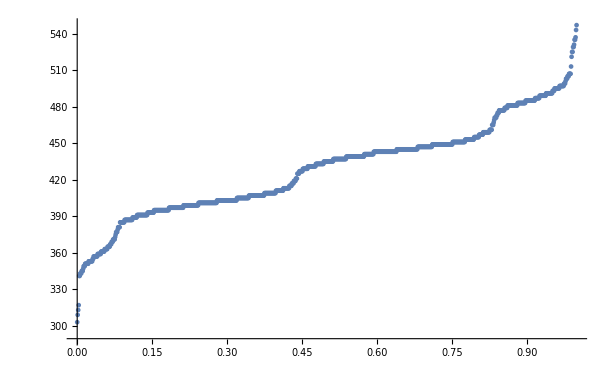

```mathematica
ListPlot[Sort[data],DataRange->{0,1}]
```

```mathematica
N@Mean[data]
```

428.8

```mathematica
cornerSwapAlg//Length
```

17

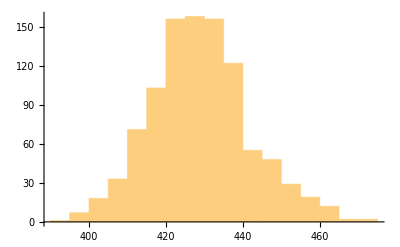

```mathematica
Histogram[MovingAverage[data,10]]
```

```mathematica
p1=makeRotations[cub,generateScrumble[]];
```

```mathematica
p2=makeRotations[p1,Join@@edgePermutaionAlgorithm[p1]];
```

```mathematica
Show[showCube[p2],PlotLabel->Style["б",Bold,30]]
```

-Graphics3D-

```mathematica
p3=makeRotations[p2,Join[{"F","R"},cornerSwapAlg,reverseRotations2[{"F","R"}]]];
```

```mathematica
Show[showCube[p3],PlotLabel->Style["в",Bold,30]]
```

-Graphics3D-

```mathematica
Show[showCube[p2],PlotLabel->Style["в",Bold,30]]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics--Graphics3D-
```

```mathematica
{{-Graphics3D- -Graphics-}}-Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

```mathematica
p=makeRotations[cub,generateScrumble[]];
```

```mathematica
Show[showCube[makeRotations[p,Join@@edgePermutaionAlgorithm[p]]],PlotLabel->Style["г",Bold,30]]
```

-Graphics3D-

```mathematica
Rest@FoldList[makeRotations[#1,{#2}]&,cub,{"R","U","R'","U'"}];
GraphicsRow[Map[Show[showCube[%[[#]]],PlotLabel->Style[{"R","U","R'","U'"}[[#]],Bold,20]]&,Range[4]],30,ImageSize->800]
```

-Graphics-

```mathematica
Row[{showCube[cub],showCube[makeRotations[cub,cornerSwapAlg]]},Style["→",30]]
```

-Graphics3D-→-Graphics3D-

```mathematica
-Graphics3D-"→"-Graphics3D-
```

```mathematica
moves=Join[rots,rots2,reverseRotations2[rots],reverseRotations2[rots2]];
Rest@FoldList[makeRotations[#1,{#2}]&,cub,moves];
TableForm[GraphicsRow[#,30,ImageSize->1400]&/@Partition[Map[Show[showCube[%[[#]]],PlotLabel->Style[StringForm["``",moves[[#]]],Bold,20]]&,Range[Length@moves]],UpTo[7]]]
```

-Graphics-
-Graphics-

```mathematica
{#[[3]][[1]],Sort[#[[4]][[1]]][[{1,-1}]]}&/@Select[cub,#["Type"]=="Center"&]
```

{{W,{{-0.5,-1.5,-0.5},{0.5,-1.5,0.5}}},{G,{{-0.5,-0.5,1.5},{0.5,0.5,1.5}}},{O,{{1.5,-0.5,-0.5},{1.5,0.5,0.5}}},{B,{{-0.5,-0.5,-1.5},{0.5,0.5,-1.5}}},{R,{{-1.5,-0.5,-0.5},{-1.5,0.5,0.5}}},{Y,{{-0.5,1.5,-0.5},{0.5,1.5,0.5}}}}

```mathematica
cub
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Show[Graphics3D[{FaceForm[Opacity[.4,Black]],Cuboid[0.999{-0.5,-1.5,-0.5},0.999{0.5,1.5,0.5}],Cuboid[0.999{-0.5,-0.5,1.5},0.999{0.5,0.5,-1.5}],Cuboid[0.999{1.5,-0.5,-0.5},0.999{-1.5,0.5,0.5}]},Lighting->{{"Ambient", White}}],showCube[Select[cub,#["Type"]=="Center"&]],Lighting->{{"Ambient", White}},Boxed->False]
Export["core.png", a]
```

-Graphics3D-

core.png

```mathematica
Select[cub,(#["Type"]=="Center") ||( Sort@#["Colors"] == {"R","W"})&]
```

{cubie2[km,{R,W},{R,W},{{{-1.5,-1.5,-0.5},{-1.5,-1.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}}],cubie2[km,{W},{W},{{{-0.5,-1.5,0.5},{-0.5,-1.5,-0.5},{0.5,-1.5,-0.5},{0.5,-1.5,0.5}}}],cubie2[km,{G},{G},{{{0.5,-0.5,1.5},{0.5,0.5,1.5},{-0.5,0.5,1.5},{-0.5,-0.5,1.5}}}],cubie2[km,{O},{O},{{{1.5,0.5,-0.5},{1.5,0.5,0.5},{1.5,-0.5,0.5},{1.5,-0.5,-0.5}}}],cubie2[km,{B},{B},{{{-0.5,-0.5,-1.5},{-0.5,0.5,-1.5},{0.5,0.5,-1.5},{0.5,-0.5,-1.5}}}],cubie2[km,{R},{R},{{{-1.5,-0.5,-0.5},{-1.5,-0.5,0.5},{-1.5,0.5,0.5},{-1.5,0.5,-0.5}}}],cubie2[km,{Y},{Y},{{{0.5,1.5,0.5},{0.5,1.5,-0.5},{-0.5,1.5,-0.5},{-0.5,1.5,0.5}}}]}

```mathematica
{#["Colors"],#["Position"]}&[First@Select[cub,#["Colors"] == {"R","W","G"}&]]
```

```mathematica
{{"R","W","G"},{"R","W","G"},{{"R","W","G"},{"R","Y","B"}},{{"R","W","G"},{"O","W","B"}},{{"R","W","G"},{"O","Y","G"}}}
```

```mathematica
{#["Colors"],#["Position"]}&[First@makeRotations[Select[cub,#["Colors"] == {"R","W","G"}&],{#}]]&/@{"R2","U2","F2"}
```

{{{R,W,G},{R,Y,B}},{{R,W,G},{O,W,B}},{{R,W,G},{O,Y,G}}}

```mathematica
{#["Colors"],#["Position"]}&[First@makeRotations[Select[cub,#["Colors"] == {"R","G"}&],#]]&/@{{},{"R2"},{"F2"},{"F2", "L2"}}
```

{{{R,G},{R,G}},{{R,G},{R,B}},{{R,G},{O,G}},{{R,G},{O,B}}}

```mathematica
{{{"R","W"},{"R","W"}},{{"R","W"},{"R","Y"} },{{"R","W"},{"O","W"}},{{"R","W"},{"R","Y"}}}
```

{{{R,W},{R,W}},{{R,W},{R,Y}},{{R,W},{O,W}},{{R,W},{R,Y}}}

```mathematica
{ {{"R","W"},{"R","W"}},{{"R","W"},{"R","Y"}},{{"R","W"},{"O","W"}},{{"R","W"},{"R","W"}}}
```

{{{R,W},{R,W}},{{R,W},{R,Y}},{{R,W},{O,W}},{{R,W},{R,W}}}

```mathematica
{#["Colors"],#["Position"]}&[First@Select[cub,#["Colors"] == {"R","W"}&]]
```

{{R,W},{R,W}}

```mathematica
core=Graphics3D[{FaceForm[Opacity[.4,Black]],Cuboid[0.999{-0.5,-1.5,-0.5},0.999{0.5,1.5,0.5}],Cuboid[0.999{-0.5,-0.5,1.5},0.999{0.5,0.5,-1.5}],Cuboid[0.999{1.5,-0.5,-0.5},0.999{-1.5,0.5,0.5}]},Lighting->{{"Ambient", White}}];
```

```mathematica
a=Show[Graphics3D[{FaceForm[Opacity[.4,Black]],Cuboid[0.999{-0.5,-1.5,-0.5},0.999{0.5,1.5,0.5}],Cuboid[0.999{-0.5,-0.5,1.5},0.999{0.5,0.5,-1.5}],Cuboid[0.999{1.5,-0.5,-0.5},0.999{-1.5,0.5,0.5}]},Lighting->{{"Ambient", White}}],showCube[Join[Select[cub,(#["Type"]=="Center") &],{cubie2[{"R","W","G"}][{"R","Y","B"}]}]],Lighting->{{"Ambient", White}},Boxed->False,ImageSize->500];
b=Show[core,showCube[Join[Select[cub,(#["Type"]=="Center") &],cubie2[#[[1]]][#[[2]]]&/@{{{"R","W","G"},{"R","W","G"}},{{"R","W","G"},{"R","Y","B"}},{{"R","W","G"},{"O","W","B"}},{{"R","W","G"},{"O","Y","G"}}}]],Lighting->{{"Ambient", White}},Boxed->False,ImageSize->500];
b
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
a=Show[core,Graphics3D[Polygon/@Flatten[Join[(*Select[cub,(#["Type"]=="Center") &],*){},cubie2[#[[1]]][#[[2]]]&/@{{{"R","G"},{"R","G"}},{{"R","G"},{"R","B"}},{{"R","G"},{"O","G"}},{{"R","G"},{"O","B"}}}][[;;,4]],1]],Lighting->{{"Ambient", White}},Boxed->False,ImageSize->600,Background->LightBlue,ViewPoint->{-2.4573024120374813,-1.0465558661868277,-2.0775913156212216},ViewVertical->{-0.23228124033955241,-0.9499245576629107,-0.20901856409238576}];
```

```mathematica
b=Show[core,Graphics3D[Polygon/@Flatten[Join[(*Select[cub,(#["Type"]=="Center") &],*)cubie2[#[[1]]][#[[2]]]&/@{{{"R","W","G"},{"R","W","G"}},{{"R","W","G"},{"R","Y","B"}},{{"R","W","G"},{"O","W","B"}},{{"R","W","G"},{"O","Y","G"}}},{}(*cubie2[#[[1]]][#[[2]]]&/@{{{"R","G"},{"R","G"}},{{"R","G"},{"R","B"}},{{"R","G"},{"O","G"}},{{"R","G"},{"O","B"}}}*)][[;;,4]],1]],Lighting->{{"Ambient", White}},Boxed->False,ImageSize->600,Background->LightBlue,ViewPoint->{-1.3597171455872965,2.8668399592836034,-1.1757541970372585},ViewVertical->{-0.9761290663215738,0.19866130407994245,-0.08778229971599788}];
```

```mathematica
GraphicsRow[{a,b},Background->LightBlue]
```

-Graphics-

```mathematica
Join[(*Select[cub,(#["Type"]=="Center") &],*)cubie2[#[[1]]][#[[2]]]&/@{{{"R","W","G"},{"R","W","G"}},{{"R","W","G"},{"R","Y","B"}},{{"R","W","G"},{"O","W","B"}},{{"R","W","G"},{"O","Y","G"}}},cubie2[#[[1]]][#[[2]]]&/@{{{"R","G"},{"R","G"}},{{"R","G"},{"R","B"}},{{"R","G"},{"O","G"}},{{"R","G"},{"O","B"}}}];
Polygon/@Flatten[%[[;;,4]],1]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
cubie2[{"W"}]
```

cubie2[km,{W},{W},{{{-0.5,-1.5,0.5},{-0.5,-1.5,-0.5},{0.5,-1.5,-0.5},{0.5,-1.5,0.5}}}]

```mathematica
Graphics3D[{cubie2[{"W"}]["Show"],FaceForm[Opacity[0.7,Black]],Cuboid[0.999{-0.5,-1.5,0.5},0.999{0.5,-0.5,-0.5}]},Boxed->True,Lighting->{{"Ambient", White}},Axes->True,AxesLabel->{x,y,z},PlotRange->1.7]
```

-Graphics3D-

```mathematica
cubie2[{"R","G"}][{"R","W"}]
```

cubie2[km,{R,G},{R,W},{{{-1.5,-1.5,-0.5},{-1.5,-1.5,0.5},{-1.5,-0.5,0.5},{-1.5,-0.5,-0.5}},{{-1.5,-1.5,0.5},{-1.5,-1.5,-0.5},{-0.5,-1.5,-0.5},{-0.5,-1.5,0.5}}}]

```mathematica
{Graphics3D[{cubie2[{"W"}]["Show"],FaceForm[Opacity[0.7,Black]],Cuboid[0.999{-0.5,-1.5,0.5},0.999{0.5,-0.5,-0.5}]},Boxed->False,Lighting->{{"Ambient", White}}],
Graphics3D[{cubie2[{"R","G"}]["Show"],FaceForm[Opacity[0.7,Black]],Cuboid[0.999{-1.5,-1.5,0.5},0.999{-0.5,-0.5,1.5}]},Boxed->False,Lighting->{{"Ambient", White}}],
Graphics3D[{cubie2[{"W"}]["Show"],FaceForm[Opacity[0.7,Black]],Cuboid[0.999{-0.5,-1.5,0.5},0.999{0.5,-0.5,-0.5}]},Boxed->False,Lighting->{{"Ambient", White}}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Row[Riffle[{showCube[cub],showCube[makeRotations[cub,generateScrumble[]]]},Style["∈",70]]]
```

-Graphics3D-∈-Graphics3D-

```mathematica
a = RandomChoice[cub]
```

cubie2[km,{Y,B},{Y,B},{{{0.5,1.5,-0.5},{0.5,1.5,-1.5},{-0.5,1.5,-1.5},{-0.5,1.5,-0.5}},{{-0.5,0.5,-1.5},{-0.5,1.5,-1.5},{0.5,1.5,-1.5},{0.5,0.5,-1.5}}}]

```mathematica
Flatten@Riffle[colorToFaceForm[a["Colors"]],Polygon/@a[[4]]]
```

{FaceForm[RGBColor[1, 1, 0],GrayLevel[0]],Polygon[…],FaceForm[RGBColor[0, 0, 1],GrayLevel[0]],Polygon[…]}

```mathematica
poses = {{3,2},{11,1},{4,2},{12,2},{2,2},{9,1},{1,2},{10,2},{1,3},{9,2},{2,3},{14,2},{6,3},{15,2},{5,3},{13,2},{3,1},{10,1},{1,1},{13,1},{5,1},{17,1},{7,1},{16,1},{4,3},{11,2},{3,3},{16,2},{7,3},{19,2},{8,3},{18,2},{2,1},{12,1},{4,1},{18,1},{8,1},{20,1},{6,1},{14,1},{5,2},{15,1},{6,2},{20,2},{8,2},{19,1},{7,2},{17,2}}
```

{{3,2},{11,1},{4,2},{12,2},{2,2},{9,1},{1,2},{10,2},{1,3},{9,2},{2,3},{14,2},{6,3},{15,2},{5,3},{13,2},{3,1},{10,1},{1,1},{13,1},{5,1},{17,1},{7,1},{16,1},{4,3},{11,2},{3,3},{16,2},{7,3},{19,2},{8,3},{18,2},{2,1},{12,1},{4,1},{18,1},{8,1},{20,1},{6,1},{14,1},{5,2},{15,1},{6,2},{20,2},{8,2},{19,1},{7,2},{17,2}}

```mathematica
Column[MapThread[(el|->Graphics3D[el,Lighting->{{"Ambient", White}},PlotLabel->#2])/@#1&,{els,Range[20]}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}
{-Graphics3D-,-Graphics3D-}

```mathematica
els=MapIndexed[Partition[#1["Show"],2]&,Select[cub,#["Type"] =!="Center"&]];
```

```mathematica
Flatten[Mean/@#[[4]]&/@Select[cub,#["Type"]!="Center"&],1]
```

{{1.5,-1.,1.},{1.,-1.5,1.},{1.,-1.,1.5},{-1.5,-1.,1.},{-1.,-1.5,1.},{-1.,-1.,1.5},{1.5,-1.,-1.},{1.,-1.5,-1.},{1.,-1.,-1.5},{-1.5,-1.,-1.},{-1.,-1.5,-1.},{-1.,-1.,-1.5},{1.5,1.,1.},{1.,1.5,1.},{1.,1.,1.5},{-1.5,1.,1.},{-1.,1.5,1.},{-1.,1.,1.5},{1.5,1.,-1.},{1.,1.5,-1.},{1.,1.,-1.5},{-1.5,1.,-1.},{-1.,1.5,-1.},{-1.,1.,-1.5},{0.,-1.5,1.},{0.,-1.,1.5},{1.5,-1.,0.},{1.,-1.5,0.},{0.,-1.5,-1.},{0.,-1.,-1.5},{-1.5,-1.,0.},{-1.,-1.5,0.},{1.5,0.,1.},{1.,0.,1.5},{-1.5,0.,1.},{-1.,0.,1.5},{0.,1.5,1.},{0.,1.,1.5},{1.5,0.,-1.},{1.,0.,-1.5},{1.5,1.,0.},{1.,1.5,0.},{-1.5,0.,-1.},{-1.,0.,-1.5},{0.,1.5,-1.},{0.,1.,-1.5},{-1.5,1.,0.},{-1.,1.5,0.}}

```mathematica
poses
```

```mathematica
{{3,2},{11,1},{4,2},{12,2},{2,2},{9,1},{1,2},{10,2},{1,3},{9,2},{2,3},{14,2},{6,2},{15,2},{5,3},{13,2},{3,1},{10,1},{1,1},{13,1},{5,1},{17,1},{7,1},{16,1},{4,1},{11,2},{3,3},{16,2},{7,3},{19,2},{8,3},{18,2},{2,1},{12,1},{4,1},{18,1},{8,1},{20,1},{6,1},{14,1},{5,2},{15,1},{6,2},{20,2},{8,2},{19,1},{7,2},{17,2}}
```

```mathematica
MapIndexed[Text[First@#2,#1]&,Mean/@a[[4]]]
```

{Text[1,{0.,1.5,-1.}],Te#]]2,{0.,1.,-1.5}]}

```mathematica
(Mean/@#[[4]])&/@Select[cub,#["Type"]!="Center"&];
aa=%[[Sequence@@#]]&/@poses;
```

```mathematica
TableForm[Partition[MapIndexed[Show[{showCube[cub],Graphics3D[MapThread[Text[Style[#2,Bold,FontFamily->"Georgia",30],#1]&,{#1,8First@#2-8+Range[8]}]]},Lighting->{{"Ambient", White}}]&,Partition[aa,8]],3]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Show[{showCube[cub],Graphics3D[MapIndexed[Text[Style[First@#2,Bold,FontFamily->"Georgia",20],#1]&,aa]]},Lighting->{{"Ambient", White}}]
```

-Graphics3D-